```mathematica
Quit[]
```

#### Kernels Control

```mathematica
LaunchKernels[8]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="~/Documents/2-d-data";}];
```

The amplitude

```mathematica
(*If targeting the position, then use [ω1,ω2]*)
```

```mathematica
𝒞[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->ω2/(1+ω2-ω1),ω2->ω1/(1+ω2-ω1),ϕ1->ϕ3,ϕ3->ϕ1,ϕ2->ϕ4,ϕ4->ϕ2,M1->M3,M3->M1,M2->M4,M4->M2}]
𝒫[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->(1+ω2-ω1)/ω2,ω2->1/ω2,ϕ1->ϕ2,ϕ2->ϕ1,ϕ3->ϕ4,ϕ4->ϕ3,M1->M2,M2->M1,M3->M4,M4->M3}]
ℛ[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->ω1/ω2,ω2->1/ω2,ϕ3->ϕ4,ϕ4->ϕ3,M3->M4,M4->M3}]
𝒮[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->1/ω1,ω2->(1+ω2-ω1)/ω1,ϕ1->ϕ4,ϕ4->ϕ1,ϕ2->ϕ3,ϕ3->ϕ2,M1->M4,M4->M1,M2->M3,M3->M2}]
```

```mathematica
EXPR[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=If[ω1>1,ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,Mb,Ma,Mc,Md]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb]+ℐ1[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ2[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb],ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]]+If[ω2>ω1,ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md],ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]+ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma]+ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]]+Which[0<ω1<1&&ω2≥ω1,ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma],ω2≥ω1&&ω1≥1,ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,Mb,Ma,Mc,Md],0<ω1<1&&ω1>ω2,ℐ3[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc],ω1≥1&&ω1>ω2,ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]];
```

```mathematica
ℳ0[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=4 g^2 ω1 NIntegrate[1/(y ω1-ω2-x)^2 ϕ1[(ω2-ω1+x)/(ω2-ω1+1)]ϕ2[y]ϕ3[x]ϕ4[(y ω1)/ω2],{x,0,1},{y,0,1}]
```

```mathematica
(*𝒞[f_Symbol[arg__]]:=f[#2/(1+#2-#1),#1/(1+#2-#1)]&[arg]
𝒫[f_Symbol[arg__]]:=f[(1+#2-#1)/#2,1/#2]&[arg]*)
```

```mathematica
(*ℳ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]=((#+𝒮[#])&[(*If[1>ω1,-4 g^2 NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,1}],0]*)
ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]])+((#+𝒞[#])&[(*If[ω2>ω1,-4 g^2 NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}],0]*)
ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]])+((#+𝒮[#]+𝒫[#]+𝒞[#])&[ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]]);*)
ℐ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,λ,1},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,λ,1},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ NIntegrate[ω2/ω1 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,λ,1}]);
ℐ2[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=-4 g^2(NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,λ,1},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,λ,1},{y,x/ω1+λ,1}]-2/λ NIntegrate[1/ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,λ,1}]);
ℐ3[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=-(4 π)/Nc NIntegrate[(Mc^2+Md^2/ω2+(m^2-β^2)/(x-ω1)+(m^2-β^2)/(x-1)-(m^2-β^2)/(x-ω1+ω2)-(m^2-β^2)/x)ϕ1[(x-ω1+ω2)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[(x-ω1+ω2)/ω2],{x,λ,1}];
```

```mathematica
EXPR1[ω1_,ω2_][m_,Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]=EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md];
```

```mathematica
ℳone[ω1_,ω2_][m_,Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=EXPR1[ω1,ω2][m,Ma,Mb,Mc,Md][ϕ1,ϕ2,ϕ3,ϕ4]
```

Solve ‘t Hooft equation

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
g=1;Nc=(β^2 π)/g^2;ℂ=0;(*ℂ denotes the interchange of final states.*)λ=10^-6;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
accDetermineϕ[m1_,m2_,β_,Nb_]:=
Module[{psi,ϵ=10^-6,Kernel1,Kernel2,hMT,sMT,sMatrix,hMTUp,hMT1,hMatrix,eg,vals,vecs,func,μ,nfunc},
Kernel1[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,0,x-ϵ}];
Kernel2[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,x+ϵ,1}];
psi[n_,x_]:=psi[n,x]=Which[n==0,x^(2-β)*(1-x)^β,n==1,(1-x)^(2-β)*x^β,n≥2,Sin[(n-1)*π*x]];
hMT[m_,n_]:=hMT[m,n]=NIntegrate[psi[m,x]((m1^2-1)/(x*(1-x))*psi[n,x]-Kernel1[n][x]-Kernel2[n][x]+(2psi[n,x])/ϵ),{x,ϵ,1-ϵ},WorkingPrecision->20];
sMT[m_,n_]:=sMT[m,n]=NIntegrate[psi[m,x]psi[n,x],{x,0,1}];
sMatrix=ParallelTable[Quiet[sMT[m,n]],{m,0,Nb},{n,0,Nb}]//Chop;hMTUp=PadLeft[#,Nb+1]&/@ParallelTable[Quiet[hMT[m,n]],{m,0,Nb},{n,m,Nb}];
(*Print[hMTUp];*)
hMatrix=Transpose[hMTUp]+hMTUp-DiagonalMatrix[Diagonal[hMTUp]];
(*Print[MatrixForm[hMatrix]];*)
eg[μ_]:=Det[hMatrix-μ^2*sMatrix];
μ=Sort@DeleteDuplicatesBy[Table[μ/.FindRoot[eg[μ]==0,{μ,a,a+0.2}],{a,0,Nb^2,0.2}],SetPrecision[#,2]&];
Print[μ];
vecs=(Flatten@NullSpace[hMatrix-#^2 sMatrix,Tolerance->0.001])&/@μ;
Print[vecs];Print[Dimensions@vecs];
func=ParallelTable[Table[psi[i,x],{i,0,Nb}].vecs[[j]],{j,1,Length[vecs]}];
nfunc=ParallelTable[Quiet[func[[n]]/√NIntegrate[func[[n]]^2,{x,0,1}]],{n,1,20}];
Clear[func,vecs];
{μ,nfunc}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

Used z=(r_(2-))/(r_(1-)+r_(2-)), ω=(r_(4-))/(r_(1-)+r_(2-)), ω_1=(r_(2-))/(r_(3-)), ω_2=(r_(4-))/(r_(3-)) here.

```mathematica
ω2p[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(-√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1)(*transform ω1 to ω2, your definition, solution 1*)
```

```mathematica
Sω1[ω1_][M1_,M2_,M3_,M4_]:=(M1^2/(1-ω1+ω2p[ω1][M1,M2,M3,M4])+M2^2/ω1)(1+ω2p[ω1][M1,M2,M3,M4]);
```

```mathematica
ω1S[s_][M1_,M2_,M3_,M4_]:=(-M1^2+M2^2+s-√s √((M1^4+(M2^2-s)^2-2 M1^2 (M2^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
ω2S[s_][M1_,M2_,M3_,M4_]:=(-M3^2+M4^2+s-√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
```

```mathematica
Msum[mQ_][n1_?IntegerQ,n2_?IntegerQ,n3_?IntegerQ,n4_?IntegerQ]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,ω1,ω2,Sen,filenameacc,Determine,Mseq},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filenameacc,dir,Infinity]=={},If[ChoiceDialog["Choose to use BSW method or to use the original solution suggested by 't Hooft, ",{"Yes"->True,"No"->False}],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[n1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[n2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[n3];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[n4];
Mseq=Sequence[M1,M2,M3,M4];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
{{M1,M2,M3,M4},ParallelTable[Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];
{Ssqur,EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][mQ,M1,M2,M3,M4]},{Ssqur,M1+M2,M1+M2+5,0.05}]}
]
```

#### Calc

```mathematica
Clear["Global`g$*"]
```

```mathematica
Information["Global`g$*"]
```

```mathematica
Clear[ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3];
```

#### 2→2

The total amplitude (and the square):

Function structure is Msum[<one flavour quark mass>][(excited state)<1>,<2>,<3>,<4>]

```mathematica
Msumdat=Msum[60][0,0,0,0]
```

Wavefunction build complete.

M1=120.335  M2=120.335  M3=120.335  M4=120.335

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00156237,0.99999412489935590912343662444231040531406051741214469075202941895}. NIntegrate obtained -1.0124084426265264928720150731875577037273842363999946669937604997×10^325+7.571423293934385428619913470876556604600838954760592011474496578×10^311 ⅈ and 6.1500745408185327571585812196476930994311142903876625576364620027×10^325 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000554491,0.99999498131737150180571837556828262982833166461205109953880310059}. NIntegrate obtained 1.0789106903215756539399067736844279026059794165352324677550772078×10^351-8.0314517626623472678465448146306134211176466019315387423838804455×10^337 ⅈ and 2.3527840851541917903801634393060026103004337277935356560275510014×10^351 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00133843,0.99999618403365874843528594536137821258137137192534282803535461426}. NIntegrate obtained 3.3389221489173904037567845290590248152882902084850216142925647624×10^403-2.4658093578137061868765991235467857808909597188758079125442925835×10^390 ⅈ and 4.6482331739246791419924571395171917168185486002430248747123478584×10^402 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00121195,0.99998937410292770194884890561093371275092067662626504898071289062}. NIntegrate obtained 3.32673×10^237-2.53065×10^224 ⅈ and 1.9045×10^237 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000761786,0.9999959093525916588224546825529326365966653611394576728343963623}. NIntegrate obtained -9.6051132200740329023237099969116492511894350055026392781406845629×10^388+7.1075478150167307848221579832440902780770523610938994530899534331×10^375 ⅈ and 7.0896743780758857200013042022217711554084219455719059369602291317×10^389 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000322627,0.99999556751059056766302020162473507269851324963383376598358154297}. NIntegrate obtained 1.5329605099789709637773483756435046671063512866630949896900204544×10^372-1.1370522731331537242733674792277646103229706927951631532231012928×10^359 ⅈ and 2.0791286760963221062396869203819289525162473529948387656212652151×10^372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00140843,0.99999264532198663557271381581437186270022721146233379840850830078}. NIntegrate obtained 2.90534×10^290-2.18716×10^277 ⅈ and 6.72112×10^290 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000531435,0.99997564209965836709990603080322468798613044782541692256927490234}. NIntegrate obtained 5.21179×10^148-4.04505×10^135 ⅈ and 1.18894×10^148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.25193×10^278+9.4238×10^264 ⅈ and 4.517×10^273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9984376327435282899754043217654952968587167561054229736328125,5.8751×10^-6}. NIntegrate obtained -1.0206523749277510889760317750748566572325723126980728583343448709×10^325+0. ⅈ and 6.2001685893836724546607677739083081288267261225620767257875801243×10^325 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999445508735833141309747029712440280491136945784091949462890625,5.01868×10^-6}. NIntegrate obtained 1.0896568872172707046779330118555511416791232653308626755819060502×10^351+0. ⅈ and 2.3764195905033192230781738967619722618403599155166078623408446466×10^351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9987880504143549251043487924306418790365569293498992919921875,0.0000106259}. NIntegrate obtained 3.34652×10^237 and 1.91586×10^237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9994685649980939215995812130444164722575806081295013427734375,0.0000243579}. NIntegrate obtained 5.23225×10^148 and 1.19361×10^148 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9986615709802529358522782398921435742522589862346649169921875,3.81597×10^-6}. NIntegrate obtained 3.3748838163087070995374064260825179096722837915553955871109077285×10^403+0. ⅈ and 4.6982551646323852231086009696392171557814229735818226765183075538×10^402 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00113563,0.99999431762266821693917168535972739285000443487660959362983703613}. NIntegrate obtained -4.1116681353979917302119136855683879296202885616866657766092766928×10^329+3.0719459303756672364512865486229538109744301476428405723660178399×10^316 ⅈ and 3.1681801899743143973166200838445227995595756846177828709362654724×10^330 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99859157369678949018286517880227393106906674802303314208984375,7.35468×10^-6}. NIntegrate obtained 2.92612×10^290 and 6.76917×10^290 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000711159,0.99999510990895033427527954393229658869302056700689718127250671387}. NIntegrate obtained 1.2359225647976122290360488853190177798318642165302242123416433746×10^355-9.1934819015185902515769869507070269373129318194110082896589957173×10^341 ⅈ and 1.5095427059796628043878439222428638601601212949289055996724392143×10^355 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.26101×10^278 and 4.54963×10^273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9996773729120954230724198363855492743823560886085033416748046875,4.43249×10^-6}. NIntegrate obtained 1.5477979779755226365756898774791944202359877708131764508847066791×10^372+0. ⅈ and 2.0992930372333078522241594682273162252778202607010396274103701425×10^372 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000313582,0.99998306553507315352327840252133484000296448357403278350830078125}. NIntegrate obtained 3.80043×10^183-2.92614×10^170 ⅈ and 8.35824×10^183 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999238213597242229857715856145006227961857803165912628173828125,4.09065×10^-6}. NIntegrate obtained -9.7025377902909508004869589684468039807661906059663492336283813981×10^388+0. ⅈ and 7.1615927434416608890500083828687881409444593184723448775815117332×10^389 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000980415,0.99999037716136297471534587644886871160565533500630408525466918945}. NIntegrate obtained 9.19221×10^250-6.97359×10^237 ⅈ and 1.91112×10^251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00152159,0.99999624407568182107802922287294322689632508627255447208881378174}. NIntegrate obtained 8.0088686001142007377250099844431878562430175797665027481071278085×10^405-5.9118908375264147495007453991749285104891490800590919303537084669×10^392 ⅈ and 2.9715177877464009262624428128384506139437224797832737312789064741×10^405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00166005,0.99999300272638420943914977024116752524207640817621722817420959473}. NIntegrate obtained 1.93461×10^296-1.45423×10^283 ⅈ and 1.2696×10^296 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000794672,0.99999565148105943665231260366124677041455015569226816296577453613}. NIntegrate obtained 2.1971134286675258899778781202963447836681146876168906163881528911×10^376-1.628739022847530479509531062450007154067182417944650464749266168×10^363 ⅈ and 2.0275104980803191720925640696324115980076839886704316188572042797×10^377 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000771467,0.99999598570468640091552848560285671197789270081557333469390869141}. NIntegrate obtained 1.6134919608808904101456562067681615623165637270468220473852492401×10^392-1.1933057986716613487068371115056777995967851361151414811676945625×10^379 ⅈ and 1.38782395545298085609732564172195256169426077916660399147610666×10^392 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.49702×10^239+2.65294×10^226 ⅈ and 1.09278×10^235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -7.63218×10^285+5.7365×10^272 ⅈ and 2.95219×10^281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9996864176109286465564396362282195696025155484676361083984375,0.0000169345}. NIntegrate obtained 3.81832×10^183 and 8.3976×10^183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99886436982451245959920005379473195716855116188526153564453125,5.68238×10^-6}. NIntegrate obtained -4.1462807728675111065724490131057823567368123090967064248144775011×10^329+0. ⅈ and 3.1948099472463581964178882700141775712722406177512226352481742511×10^330 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999288840613069517283817422281799736083485186100006103515625,4.89009×10^-6}. NIntegrate obtained 1.2471772736118693018888794360748927770972875358346893365411506905×10^355+0. ⅈ and 1.5232935574929911991384939373642504664862037952078281959130745993×10^355 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.8314641724534449362200357693633980445847358108998413326693472763×10^344+0. ⅈ and 4.4780347919455916802775836759405913407341773129496360952398006904×10^339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000323297,0.99998626687297438439090354906496616038680258498061448335647583008}. NIntegrate obtained 1.75566×10^205-1.34476×10^192 ⅈ and 1.0758×10^205 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999019584815279043481239806823168692062608897686004638671875,9.62284×10^-6}. NIntegrate obtained 9.24836×10^250 and 1.92275×10^251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99847840737663501168609736513559482773416675627231597900390625,3.75592×10^-6}. NIntegrate obtained 8.0940805366817173695358884446787174115553795053657366613498877652×10^405+0. ⅈ and 3.002895513064051705745611048670035142525606711786860881136426268×10^405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -3.51894×10^239 and 1.09987×10^235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000466706,0.99999451875556660137119502004821036678094969829544425010681152344}. NIntegrate obtained 1.2641453411385848885052572666142497379945852652310336769064544712×10^335-9.4347775987725520449360793834616563680374946638534655221790449593×10^321 ⅈ and 2.7342017436653921435256309026103899811088166502352786322459654654×10^335 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000391614,0.99999524174121922094418554944131316553068700159201398491859436035}. NIntegrate obtained 3.2498953288922757969463257647438977696401771937692961451601610372×10^360-2.4154598101786076146816714163378084640708155398287955461245977381×10^347 ⅈ and 6.7837222650392935337270105970299352633216328838667206407508488757×10^360 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9983399534678728455029672606002577595063485205173492431640625,6.99727×10^-6}. NIntegrate obtained 1.94903×10^296+0. ⅈ and 1.27908×10^296 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000272255,0.99999632681766837420337122642813310058329534513177350163459777832}. NIntegrate obtained 6.0846573858245516650351029823998419101636133153480912462848401965×10^408-4.4886929839338979292674784259115571539751970653161109183355046995×10^395 ⅈ and 1.3656358674724431218434866588868316812484306766424978815137218372×10^408 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000546684,0.99999117447259905906761909191032833277290592377539724111557006836}. NIntegrate obtained 8.16994×10^261-6.18295×10^248 ⅈ and 1.39691×10^261 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -7.68912×10^285 and 2.97396×10^281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999205327546180159070492166062393835090915672481060028076171875,4.34852×10^-6}. NIntegrate obtained 2.2192800880538582096749355502383991200119340519033096980331184393×10^376+0. ⅈ and 2.0469619995230904419688243573039762163701925219102377029895671488×10^377 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999228533042036350564525648554337067253072746098041534423828125,4.0143×10^-6}. NIntegrate obtained 1.6300467452387371235043296919571248699181659473531400578434735788×10^392+0. ⅈ and 1.4019045758661100340270982415349273916985494097844895784782954659×10^392 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000632415,0.99999337422803147199681472571952678407569692353717982769012451172}. NIntegrate obtained 6.25699×10^303-4.69573×10^290 ⅈ and 1.06443×10^304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000761786,0.99999574338128326167128117870144810019894521246897056698799133301}. NIntegrate obtained 9.9396216298226079831109310284613178309445030984590090388780998184×10^381-7.3635957776995260567582956741566249132891310025185178707107839802×10^368 ⅈ and 2.2845678404579165261213251924062982606933205930551905448251882357×10^382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000843982,0.99999605670171798266428512483999790916300298704300075769424438477}. NIntegrate obtained 1.4253940860457426760198592442628367887064773136266133402553502138×10^395-1.0536751879885829317958378367584864235723105127665496682533944176×10^382 ⅈ and 2.1049499398127625361016732663604206262514580749303187870828225982×10^395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999676703102756541497765641057782204370596446096897125244140625,0.0000137331}. NIntegrate obtained 1.76479×10^205 and 1.08142×10^205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000870959,0.99998809682934831052516881904485002152682682208251208066940307617}. NIntegrate obtained 2.33351×10^223-1.78076×10^210 ⅈ and 8.56115×10^222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999533293688203170325283497543722432965296320617198944091796875,5.48124×10^-6}. NIntegrate obtained 1.2752956457976305280010426355046918703852853870415921023662882548×10^335+0. ⅈ and 2.7580007970885408154358581448519195182155184476479393274016483172×10^335 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9996083855156040704555316100954343028206494636833667755126953125,4.75826×10^-6}. NIntegrate obtained 3.2808777928599121063462270061082591305748886976939793943915218048×10^360+0. ⅈ and 6.8485272380573930144237778680070790302482099598084914159502441984×10^360 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.45726×10^293+1.09381×10^280 ⅈ and 5.96932×10^288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00348431,0.99999458333535875016243168805427088408066538249840959906578063965}. NIntegrate obtained 8.8308805966864244946271892860838044362114685955143072974928889166×10^338-6.5876591229748071635722007302684175170957476814230364744726162339×10^325 ⅈ and 1.0468444501380260777228845098497696991300702426354060270948194572×10^338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000632415,0.9999953501679695185258537498164399526245915694744326174259185791}. NIntegrate obtained 3.0453440468533833990998692315494528819245903162038944169105064611×10^364-2.2618870904573176659094924612621549306244959209782391596765758617×10^351 ⅈ and 2.6822464426450225753072819047158422295022679673956979165882633821×10^363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99972774468308135838688632812676360117620788514614105224609375,3.67318×10^-6}. NIntegrate obtained 6.1503794123759250105385669547109043193229743913952931208244063516×10^408+0. ⅈ and 1.3804124447627868918689426687969665207912055707814183666479621537×10^408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999453316265417463317745350170895335395471192896366119384765625,8.82553×10^-6}. NIntegrate obtained 8.2225×10^261 and 1.40594×10^261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -2.50176×10^212+1.90905×10^199 ⅈ and 9.94918×10^207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000745497,0.99999637621248858873962013483170652161646785316406749188899993896}. NIntegrate obtained 1.3492930222864143034479639226468752593083902233442753144162188642×10^413-9.9498206455037543694182343975802409416083810483380292255094306754×10^399 ⅈ and 2.1914508873201898609755450932293837107256995264470496138857170788×10^412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000559466,0.9999917748545467624938083662719523481143824028549715876579284668}. NIntegrate obtained 1.22013×10^271-9.21519×10^257 ⅈ and 5.09644×10^270 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99936758460860508081723130313633873811340890824794769287109375,6.62577×10^-6}. NIntegrate obtained 6.30498×10^303+0. ⅈ and 1.07263×10^304 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.46842×10^293 and 6.01462×10^288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999129041441257466945984055950447100258315913379192352294921875,0.0000119032}. NIntegrate obtained 2.34666×10^223 and 8.61093×10^222 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -2.51579×10^212 and 1.00063×10^208 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000534455,0.99999365789040359862634973825076811770884432917227968573570251465}. NIntegrate obtained 7.6798415712580582903751458993524132643313839790219619096642523383×10^310-5.75639×10^297 ⅈ and 1.0860144758997338772538287925919813720637767337135209573934262126×10^310 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999238213597242229857715856145006227961857803165912628173828125,4.25662×10^-6}. NIntegrate obtained 1.0040852861386513072933037378209034723165415542712012964682727169×10^382+0. ⅈ and 2.3078568506308000281001940672526161402492947712832234958291078047×10^382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999156017599973281912394129644638951504020951688289642333984375,3.9433×10^-6}. NIntegrate obtained 1.4401961791108364129760394550724177187623720815113527894868163259×10^395+0. ⅈ and 2.1268838775186761638248268903380176921360798959768741300557909556×10^395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00136765,0.99999642181040230333852715451266324198087431796011514961719512939}. NIntegrate obtained 9.6919896258923206741235456908418128749706106646931834893679216207×10^415-7.1444161274562078522549274027092174486732201122735825543274454719×10^402 ⅈ and 2.1056113051334706712575008534856065554977678513035864682760620295×10^416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00038623,0.99999583597939195651452438809783651585405550576979294419288635254}. NIntegrate obtained 1.1521769575378665306652763292488917666698162265778409923797291878×10^385-8.5303475237457385814159349788159641226425740271916991087319821276×10^371 ⅈ and 6.1147230657871687608012866458532776124570157426228450165993810769×10^384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00100802,0.99999612313062796981475219412413557584784484788542613387107849121}. NIntegrate obtained 2.1714696800787021816529506959968157765713756227188529258699197045×10^400-1.6043576280502172943658167769803867976300196443998584126922678819×10^387 ⅈ and 1.7756194027700429404764490319273416838165277636308767611305252093×10^400 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9965156941454152250518816469337934904615394771099090576171875,5.41666×10^-6}. NIntegrate obtained 8.9079200002410743484965967178266967373988073763269602671447065226×10^338+0. ⅈ and 1.0557707813649966709658487474065239922736540487739104326493737979×10^338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99936758460860508081723130313633873811340890824794769287109375,4.64983×10^-6}. NIntegrate obtained 3.0742998268004501018470480531188867452488724928559471701499447411×10^364+0. ⅈ and 2.7078222785543893085134647377226929987604607922204442729493482253×10^363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00185962,0.99999479768584655370582559702485880848144006449729204177856445312}. NIntegrate obtained 1.6355899715952476009115620788936463877466062090996896931222477883×10^345-1.2188276137535031542150978182367843654105538695586551400616679582×10^332 ⅈ and 3.1096183212203042754192034388237891392650405644082114107189424442×10^345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00119103,0.99999544710901143057364616646698340929333426174707710742950439453}. NIntegrate obtained -1.4072289271825336396401217862617104662551642200481171681328741849×10^368+1.0445563873423077288909316910343216243048423031863846159764521979×10^355 ⅈ and 1.7743894073968919044338412125682870072770724254273338774811645932×10^369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99925450302689035396268291133736738629522733390331268310546875,3.62379×10^-6}. NIntegrate obtained 1.3649167800911224663705906421028341243237702042369092124903581745×10^413+0. ⅈ and 2.2166176551940858893836470946054898243149837055021392838546599596×10^412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999440534216322294495948863612966306391172111034393310546875,8.22515×10^-6}. NIntegrate obtained 1.22844×10^271 and 5.13104×10^270 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000630022,0.99999663711586608039966417782115626344818792858859524130821228027}. NIntegrate obtained 6.8491424440794635615969935128469141774009871635045691760377014986×10^427-5.039990344996384331960235238497249215904330716105017932668291014×10^414 ⅈ and 5.0199249896203461460521260284833699180450149499514779197972680374×10^427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00143359,0.99999221722831863147933930107552624733102675236295908689498901367}. NIntegrate obtained 3.09141×10^280-2.33105×10^267 ⅈ and 4.5603×10^280 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999465545022593020792374407523794843655196018517017364501953125,6.34211×10^-6}. NIntegrate obtained 7.7406592965315410142035913671020039350116589023927700499975034271×10^310+0. ⅈ and 1.0946112563841936900853007732218018624693866916197667688590152522×10^310 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9986323476458911531372653058724608854390680789947509765625,3.57819×10^-6}. NIntegrate obtained 9.7943395226360571586944018705713891869688950631865827979678843619×10^415+0. ⅈ and 2.1277593434124306434549003516397271296391852366211280838567572325×10^416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00113198,0.99999388073410828591221016174023228373357596865389496088027954102}. NIntegrate obtained 2.7225025143582314316288160059343948183688670008584976323009101605×10^317-2.0385×10^304 ⅈ and 3.7416693120420463101282411494886764518648658099554785085901790046×10^316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0018648,0.99999646794651717136158638782501839603611415441264398396015167236}. NIntegrate obtained 4.6929441394302385809346714599509109585671731410528393863150936508×10^418-3.4580106860436664920897834726126438539876273389868600749902467554×10^405 ⅈ and 6.7747644015306530597901371259795836996580034927388350873349150528×10^417 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -2.8543141461899497783353398972584332999967435994363011707274746941×10^416+2.1005921284912294014342951300523280214096360163580645016599068119×10^403 ⅈ and 8.2405755403757290617560282829102390560136656197932801928332876463×10^411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99961377036646285073988316138837717517162673175334930419921875,4.16402×10^-6}. NIntegrate obtained 1.1636415862835722865601312898846226790833870629364526075747898804×10^385+0. ⅈ and 6.176277262139593339091405220757460531388269127627976203558801393×10^384 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -5.20756×10^269+3.92637×10^256 ⅈ and 1.73472×10^265 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9981403778564318057635318393039369766484014689922332763671875,5.20231×10^-6}. NIntegrate obtained 1.6498679305570841078789687967258039073165799023515081739975719386×10^345+0. ⅈ and 3.1366619475097891500618298548947329141163798694038124202605874561×10^345 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99899197672893792310060134820304256209055893123149871826171875,3.87687×10^-6}. NIntegrate obtained 2.1944103498813289614254451736405345531507402891721305456750686564×10^400+0. ⅈ and 1.7948721019056430719273756470054084900065067180255282026203646082×10^400 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9988089720059774747999703503609225663240067660808563232421875,4.55289×10^-6}. NIntegrate obtained -1.4206276652307818250153909892535325681106321160366978170447941911×10^368+0. ⅈ and 1.7912806597785499845723423913139126858496833390513629775565779206×10^369 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000841357,0.99999680667716467913722574209316185100959728515590541064739227295}. NIntegrate obtained 2.072583952806061402655936061907456309237572699608754472457443845×10^440-1.5229021350072844636736368401851988550461579597199679292783790866×10^427 ⅈ and 4.86040852448989879848235391905739859622019801561421011731787091×10^440 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00321563,0.99999692968852958686988978182115517245875935259391553699970245361}. NIntegrate obtained 5.531490430866923805979722265221796691128664454776793374873126861×10^447-4.0599538697866991762987202170070807325013529225711341414027519366×10^434 ⅈ and 9.6832588933696117136402247394440144750878337988635172483489216088×10^447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00135074,0.99999708766068827356630029155708239141375770486774854362010955811}. NIntegrate obtained 3.7292863267151519655732933001225104349404993321592774220150112092×10^458-2.7332767805880222030884617776626432239672952839423218494610738892×10^445 ⅈ and 2.0423891081421551126366708451443845575286083034333710444442889042×10^458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00185081,0.99999720258082947699699354819451169174016058605047874152660369873}. NIntegrate obtained 1.1822645229239211336247430595992897203024427983940181795089171093×10^468-8.655351725579798008755157066726173689627743576499209763617910053×10^454 ⅈ and 7.3931595289001292332012569145096554751179350750507002940380029618×10^467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.7184774795263853181969517920017592156593458586134010681650881978×10^407+2.7398992175595310012964599449996183549222060462294970510301467993×10^394 ⅈ and 1.2042251633191682389064909665433567505766473762645061628837156131×10^403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9993699780231006320370401585506670016911812126636505126953125,3.36288×10^-6}. NIntegrate obtained 6.9278149930127193085421326986773749052743364572951439591740769207×10^427+0. ⅈ and 5.0775955533649266805349876281892859262421314488964678633531093458×10^427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -2.8869059762340904462625367214528682874095650470648634851068743632×10^416+0. ⅈ and 8.3373942107164168848050838399040716534885581025555637460379579077×10^411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99856641021595529315001138481733278240426443517208099365234375,7.78277×10^-6}. NIntegrate obtained 3.11301×10^280 and 4.59216×10^280 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -5.24418×10^269-5.59169×10^223 ⅈ and 1.74684×10^265 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00119931,0.99999667276118841152432762872659388619922538055106997489929199219}. NIntegrate obtained 9.8203688635964557290224593679720788978345173860597556413789171262×10^429-7.2240948748962893967904749399730878215092706833716146582598234237×10^416 ⅈ and 5.346262510778407560372766370167635863579701426333613528996361403×10^429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.1288953342356058880096198833189682400655219688798323818799596529×10^438+8.2842944388430225916664916266733560471639332889513759191099400876×10^424 ⅈ and 2.5818079715273757447329217005487726952780075746771443194603358396×10^433 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0021818,0.99999730886569897688132547140284211995009400197886861860752105713}. NIntegrate obtained 1.5401310130366970315682008042509179685259456708580040107824257841×10^477-1.1263369164235678774570323050228930287905127398735488161680399647×10^464 ⅈ and 2.676417168469090761114909546787225983856729349176547132076940228×10^477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.7520672971182231960100512229430615167891992724213171714050993054×10^457+1.2826464151580518486867986817384251813071177779272689121280225114×10^444 ⅈ and 5.2517224586144278139844835315513361790435624737778411702178909631×10^452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.9832964098000943847272461244299410195610941566549717769062816006×10^427+2.9270844620295615764320705207523870865603567692144297716573265665×10^414 ⅈ and 9.6622314660209311397415309164292813212229734354771869444209911369×10^422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99813520133098957245500193469212035779491998255252838134765625,3.53205×10^-6}. NIntegrate obtained 4.7453034777688162678371552309302024976757875128920695921986348323×10^418+0. ⅈ and 6.8503511290212461429543499698879384965990733315588064430024912553×10^417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -8.0969997772132149712977132498742154519711070554934383615259570004×10^447+5.9344820758705149956211626872729601365257123917226796172709926484×10^434 ⅈ and 2.1478437677632957695006132255731183521134609205510736930984181722×10^443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -3.7598145847069270578662999230855238844586035373379858982588284791×10^407+0. ⅈ and 1.2179347510619608627035111300545769087558597839244148918709935752×10^403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99886801705415057613286766713400766093400306999683380126953125,6.11927×10^-6}. NIntegrate obtained 2.7439720375153744240249891536862249718459721283609442614781328341×10^317+0. ⅈ and 3.7711430064533723835095405476684691218384438795726604261506803593×10^316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00148882,0.99999652499426120248667907417818023763089740896248258650302886963}. NIntegrate obtained 4.5133099039102561292773643680447393880651340257132632837284387359×10^421-3.3241926641835440642036467125795245822807463467381969968192948302×10^408 ⅈ and 2.9920372718416857319083944095841987038968635271074830342027419881×10^421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -2.0546306000917392965080157799195930060640810085409727610102948196×10^419+1.5114925132727091812114071489678079957651106981034610802911469641×10^406 ⅈ and 5.6925180301761406023034060492646351469450324232033261200776845255×10^414 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000329729,0.99999742383163434259537184073396431926994409877806901931762695312}. NIntegrate obtained 3.2683719800953414598960752241409154766067827909489586182207926233×10^485-2.3876165870202573191113048161004574500372101350879058102425979195×10^472 ⅈ and 2.2408073721899427326886511674539809663803036938131652863928394432×10^484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9967843674198844862617552298189593784627504646778106689453125,3.07031×10^-6}. NIntegrate obtained 5.5985398074248482554366782129595002190750221604671664293638543089×10^447+0. ⅈ and 9.8007516957773877370897518271923825551862816819703537566609691013×10^447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.142638872082047720058578388855873552131918020643217108887234421×10^438+0. ⅈ and 2.6118764634968298265766481845421919571823953748058934237626423076×10^433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99814918934832366141478299237377314057084731757640838623046875,2.79742×10^-6}. NIntegrate obtained 1.1974583579085744404961131260001766146572814466796461129960803668×10^468+0. ⅈ and 7.4872957111693784120990172049331042959693825357053477567426378083×10^467 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.7746228552775699520374282682609040214885897607116668198664088522×10^457+0. ⅈ and 5.3170212899377084433594004174198894187114932796221050276589861579×10^452 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.3191439279468535351545706901847562352557455772445951655473144348×10^466+9.6467462924205710272109484244054736279343468488502743962209484095×10^452 ⅈ and 2.8757568685939633292591170516332021260317914205720309124790354411×10^461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9991586429970635697787872953057330960291437804698944091796875,3.19332×10^-6}. NIntegrate obtained 2.0956702092695341897514124210947006366464644570492520906163981843×10^440+0. ⅈ and 4.9145051147851597882512787199521126053656805028690783426506045654×10^440 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -4.0303171443479101912327108410121796383193036682002154991336241218×10^427+0. ⅈ and 9.7805021285528389287820769706543219338211907888522523078874727668×10^422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000835776,0.99999699368832929334529257495850496084699443599674850702285766602}. NIntegrate obtained 1.3946440410081559571854720956684958640972265822816774841930602922×10^452-1.0230407462545925398050632505885623656357764838862398951164633287×10^439 ⅈ and 2.5488835377265751899092892168849498716982525511906969494276661021×10^452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9986492608635207063154382023384414424072019755840301513671875,2.91234×10^-6}. NIntegrate obtained 3.7758027151033335466319640212961391745126833134855110803017624458×10^458+0. ⅈ and 2.0674745798888567985870307288005101997522173414922051369721097271×10^458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000322627,0.99999724714138547455121423671378644293383786134654656052589416504}. NIntegrate obtained 1.2278408618775256213120643270390985639874162697803238802095140731×10^470-8.9854914135334240987616617063835007494031806585194512113842698144×10^456 ⅈ and 1.7277418030436294887284702764412981844782630421927327130072252114×10^469 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -8.1984563724166328301638801222410862783555932862362866284987101546×10^447+0. ⅈ and 2.1737309489432205257680131583016815710805703668570488633632833451×10^443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.8603275097648714652321578862970399751431610088002667468596639157×10^410+2.8432332266571251119902997507602957070871518704393701567787138314×10^397 ⅈ and 1.2048990241162562426554178359217499978216413938597363716360519031×10^406 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.998800692852049484295184900162212215946055948734283447265625,3.32724×10^-6}. NIntegrate obtained 9.9334224754697944041054981665755157032698014400236254421622068765×10^429+0. ⅈ and 5.4078597561226838908007413596708546253004976013839014220502398942×10^429 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000313582,0.99999685307884075934260030018262133122419754727161489427089691162}. NIntegrate obtained 1.5634946972625488717772682695859797547442443722848822225271745375×10^441-1.1484056653838332964042075736607891089399057459170761533629293985×10^428 ⅈ and 3.8086238834481378797538083735924774157811480430485400932289994053×10^440 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -2.0782929778564081339147029527128530610901754922505449435152081454×10^419+0. ⅈ and 5.7600931297838478137093327734842266627362800434272778158212400888×10^414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00255478,0.99999710534146572750808788549066463691161743554403074085712432861}. NIntegrate obtained -1.5620029952222986785345794276120776428353297393308214524868473209×10^461+1.1446121283947210862435857466196642533147730322402191746253054725×10^448 ⅈ and 1.1121561804683870727808490379072228411204188828237127739186066632×10^462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.8869610394245008397920097037860431707057945843071781705398534128×10^474+2.8396307049099077171444379884461524243626052701116117370778286985×10^461 ⅈ and 8.4223215981679175325647003674295350017349468395243657419500042008×10^469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000630022,0.99999672633105354629876659129823768257239180456963367760181427002}. NIntegrate obtained -1.5797965092558695706382245847103772379406635093429973412041578982×10^434+1.1616159275972433217533129689190008895130735750928361385813640138×10^421 ⅈ and 9.9335371441156419112204777628055443195858799777357018937160343043×10^434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99781820373173544906630905160227484884671866893768310546875,2.69113×10^-6}. NIntegrate obtained 1.5605045723011770963491680291840786961771126045876405053496527185×10^477+0. ⅈ and 2.7118779324227649614052748112647247144788406391674471547697026851×10^477 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.3365650134862442558769113975084944358401781199179413088898722655×10^466-3.8717931324932802740532903274375393537287270388240590697753620694×10^419 ⅈ and 2.9119313163442684742908240810139501040227875854619510377983973924×10^461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.7089449532281702318702360997624873407018145226211936985091543768×10^440+2.7208981420864862629669263629482406972166012721918502380661843521×10^427 ⅈ and 8.8281372589530746186717641834682843171351512484137414888340019377×10^435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.188305362980936387110469010803530674508955629160611435620753496×10^459+2.3334371781370694097216629334462587601208107387367681295781030899×10^446 ⅈ and 9.8205296834119516518636448048660804815852015479479654002613428573×10^454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99851118189898923596832525095834398598526604473590850830078125,3.47501×10^-6}. NIntegrate obtained 4.5639171611578495308262301012709672991255296681186810435942098911×10^421+0. ⅈ and 3.0256063170801680819184076978770691196977715619957144381143509051×10^421 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -3.9036347086352071533680562077017238187300298889811916877462414107×10^410+0. ⅈ and 1.2187626715682735437902593499639257093795658058340100313889830645×10^406 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00155655,0.99999733966675559396028951275776919249693719393690116703510284424}. NIntegrate obtained 6.5079382620078646078900073110553386367007288142020560944028323551×10^478-4.757813270728157190481353560259454616010806365107579287285219635×10^465 ⅈ and 2.3745279060776679589595968769905994203659692713183041707943630621×10^479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.8798763377985105480498066865088179272159629850379372719209556054×10^430+1.3809224853078583965347238099679163420914540264049111710531589622×10^417 ⅈ and 4.3475969163984429086590540790798792603960041660825325828164451685×10^425 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00155276,0.9999965740377257390883908349035746887523146142484620213508605957}. NIntegrate obtained 1.3868878760399264202799484117574077027926381582193797952104892418×10^424-1.0210708477052049760313081009642144082045752674475408359804965219×10^411 ⅈ and 5.0034307764556075551647218969853707128189479156762763273806017755×10^423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.9421728088085276573818029235011167327122179115807021828105479526×10^450+1.4230408385118744498787217121110433903404278531124850799301228568×10^437 ⅈ and 5.3232665901741820154448697940402521510615701173546922316134469894×10^445 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.3222705744121778513760569506945314335971247787313300315407902767×10^422+9.7236408477779662010674222350237390874707655826461233324252591569×10^408 ⅈ and 3.5103046155103825499327909151404474526087441122123263584636644239×10^417 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999670270971492000151685519693245396410929970443248748779296875,2.57617×10^-6}. NIntegrate obtained 3.3126144729423440264207655988669974104589919158225065383094725508×10^485+0. ⅈ and 2.2707231133139495843557254582999366439104132213089147695706899861×10^484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -3.9395490376325307223107593933032085308804891042787792601728857639×10^474+0. ⅈ and 8.5306428068222141530072171681211114184711194432454932270560406248×10^469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999164223641935265898643414583801813932950608432292938232421875,3.00631×10^-6}. NIntegrate obtained 1.4111989175006383213587689934243938347501509643855878409762969676×10^452+0. ⅈ and 2.5788296653823049034042834157151717184376935924792514646615829991×10^452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -3.754433384441732305810584679248077941327518076034308940022277605×10^440+0. ⅈ and 8.9318737401441861584524478152390848913292640011904706233870193182×10^435 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9996773729120954230724198363855492743823560886085033416748046875,2.75286×10^-6}. NIntegrate obtained 1.2438416008018027364661875224407218857351124873155511732211419582×10^470+0. ⅈ and 1.7502595063188106015192802280114557528795961828552591757081988255×10^469 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -3.2296188460616373878009187601540271952275218933928043199881652695×10^459-9.6639157748116111305023736497722880077403717415827675523535609616×10^412 ⅈ and 9.9435362496471937781606731941828983102691269467250903195609555618×10^454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000988541,0.99999744084748660524664768951656756978962903303909115493297576904}. NIntegrate obtained 3.2041433971183572109217421129177143109136456262554654990434326337×10^487-2.3401479083841723708805095711373011710935058085857850793632805663×10^474 ⅈ and 8.0916296171715266592495584409488972893391409019079232616888451178×10^486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000538284,0.99999703403373721018553604475941065654609474222525022923946380615}. NIntegrate obtained 6.6593571094326992170670325787457757052673807502787328217149098631×10^454-4.8831701755618834625989525304412469252634390234763051878611466461×10^441 ⅈ and 1.5224641136255474013925769913442414018009255436465165633914100902×10^455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00119103,0.99999726646107717870064297209335701932531037527951411902904510498}. NIntegrate obtained 4.5999022610616527668457726357881257344426508065545388321886791968×10^473-3.3654645028708456865972030765545482828189259821942334109311487277×10^460 ⅈ and 1.0600966641419665138916731101624251446033381861520199377698502256×10^473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.5281016439614383357131208444110111528159416810135449394703767739×10^413+2.5974847689601637863553056250049618885497883543572639403542767117×10^400 ⅈ and 1.0598465768124730964648654518945425943519707383209885123640949348×10^409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.8794206805842828541167569514565461839283910889028111254692569904×10^468+1.3740442681955691450231632923677603492357935358175401685410646422×10^455 ⅈ and 4.0907721042998821045390397725451135922836382521851176297271109571×10^463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9993699780231006320370401585506670016911812126636505126953125,3.27367×10^-6}. NIntegrate obtained -1.5980807135199031105646702728258251208035344800880132002373408366×10^434+0. ⅈ and 1.0048532895369021334012650219666531786068347614709183137727230702×10^435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9996864176109286465564396362282195696025155484676361083984375,3.14692×10^-6}. NIntegrate obtained 1.5819976736352840832027634535552548045225256513193423659821147073×10^441+0. ⅈ and 3.8539106629783390126632964977473442862918037113553505757949992806×10^440 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.3376269495582650510075379654535542677118935028009944285542252358×10^422+0. ⅈ and 3.5524045009078256027028100123637906344213091270876057537918651133×10^417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.9022437906917608351982393194835828803228204002402752100774371035×10^430+0. ⅈ and 4.4013592335109580732716754452359012852587318234479580472615305747×10^425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9974452233672665584819638784352946458966471254825592041015625,2.89466×10^-6}. NIntegrate obtained -1.5819080837282200134989974696442950506744962971703738594827564875×10^461+0. ⅈ and 1.1262967718140708613277675723000073795013712991249775968273464158×10^462 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.9666774407448948503745827554054356080307641757527098200079464959×10^450+0. ⅈ and 5.3879443828738035631914939264547504487497052978951112630573045892×10^445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000466706,0.9999967703787286994886562125316176175005011828034184873104095459}. NIntegrate obtained 1.6281729175134646284020410537924891308389254072412817183962807489×10^436-1.1967345538591300408466598270296521251062406102317617394159691389×10^423 ⅈ and 2.9311895735308954137800453017372726899371937168624380945888504277×10^436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00113563,0.99999688383244877361896284923004074585151101928204298019409179687}. NIntegrate obtained 1.0525775760721920322112283210372293936675189960150773898574452586×10^444-7.7288872399682533342299315185567500137060945192270719149007769327×10^430 ⅈ and 2.1148675794844918715922548099488798874646041857256079494978389431×10^443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.1218320219070807621949172098111069722339518754485647286048660658×10^443+8.2272108219033695774708032981221149503187656926166112260549826473×10^429 ⅈ and 2.7734725137763216546452267055352005143592584025568124180962330874×10^438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000979541,0.99999715346663469781804129809382741811418782162945717573165893555}. NIntegrate obtained 1.7245615188603421517618883157187284185507475142712848575395645487×10^464-1.2631514827282361671338182633648951213590082490703248622311856419×10^451 ⅈ and 2.2484674073060064539050850331153839243290017368481787709990394677×10^463 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -5.4427509513870262647713858383471664145730085998650852130850416346×10^461+3.9823260022593656615242211738085863975162996016951868499544985642×10^448 ⅈ and 1.1903575577280771618684157688122832355695402597762922403339824288×10^457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -4.450746306795193013349484467989729201029935895157038635677890259×10^476+3.2507201234704748728410756159668421861977498885515358394035358143×10^463 ⅈ and 9.6299720692937855698739913153583421469321681198443826656421487839×10^471 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9984472364949005048113950255839199598995037376880645751953125,3.42596×10^-6}. NIntegrate obtained 1.402611520031969803423047227411495943308735848128987420419183705×10^424+0. ⅈ and 5.0600794448921188615436529896770228740760502116307746011490994143×10^423 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -3.568036586701844229134299186182700976395748871127606178377523761×10^413+0. ⅈ and 1.0721699288790078118306369671016031758609079565647076837750729961×10^409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99844344732571384368365052797145153817837126553058624267578125,2.66033×10^-6}. NIntegrate obtained 6.5946450803674637157928084714826773459935626914792868465898425394×10^478+0. ⅈ and 2.4060338052828932811020775648846247309488943851724137053582160134×10^479 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.9043943635112701648766005509371036091782577020308111193589216299×10^468+0. ⅈ and 4.1425242780289326701864570007987004244390986680818255746908399082×10^463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00080829,0.99999750828863535345981692421986342100836964164045639336109161377}. NIntegrate obtained 1.0550704778499307455660857461415513070113141614484476489547357002×10^494-7.7000154982299623079190004114380029697831549110934531223580655172×10^480 ⅈ and 1.6659861813633730463150720216012050406063560127635248439763902751×10^494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -7.6421052535216515836508186207062460104590367789082609269806720885×10^424+5.6177418156917875905954712361130957594212278896968364026070013449×10^411 ⅈ and 1.9408996382665231049286795478570399335343070138134595763952873459×10^420 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00114359,0.99999736853225692888680971228548832741012120095547288656234741211}. NIntegrate obtained 1.5241130806973435901225038940789957330089256631384723887891983462×10^481-1.1139695074541798741733944952058743333782707985266569983247044309×10^468 ⅈ and 8.2276649869597554372694209455302929413906269967419394004364265885×10^480 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99946171565248053563802754784006765476078726351261138916015625,2.96597×10^-6}. NIntegrate obtained 6.7410675403181028018468823745045531042729223068244306112477622791×10^454+0. ⅈ and 1.5411382023190991415431068521489279177554142294043674723571632539×10^455 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.135690990413897086041281173068401396564546798021151698218463777×10^443+0. ⅈ and 2.8063467073733855949592608666093766034474811664216453721589440825×10^438 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9988089720059774747999703503609225663240067660808563232421875,2.73354×10^-6}. NIntegrate obtained 4.6584748516153013486959404669029572285210929071149723071278867709×10^473+0. ⅈ and 1.0737420961295694298566961577393118540325932615407261022999770766×10^473 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -5.5137315125521809187002303550101522440274975875724395417173505553×10^461+0. ⅈ and 1.2051604845820502138678884644209301046357049624808499014301300001×10^457 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -8.06290113387012444789534976028265270278691806644868299445328307×10^432+5.9208234936059736806482270958602536006016695358319234054483996197×10^419 ⅈ and 1.7745627531617528421209429878102123118402215307997309894305194755×10^428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -4.3334189256626030975245632310697835340836540995409223794436532828×10^452+3.1741935661465211530231599407819917128525207501916074486260643598×10^439 ⅈ and 1.2253953232381627163818730583170669499280418782235912398656839675×10^448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99901145945376906994626897695610523442155681550502777099609375,2.55915×10^-6}. NIntegrate obtained 3.2474477947094046227820588134102016901214057850513643952245613066×10^487+0. ⅈ and 8.2011543698713204377582266669443245916063204718040289816460509656×10^486 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00243926,0.99999704258343496405477847637638388889058660424780100584030151367}. NIntegrate obtained 6.3705779908173619101909532839085946637185307053178197832663542318×10^455-4.6710980573440283551911141915450414702537428900619382531447626063×10^442 ⅈ and 1.1086894853851925292846121303520568443005167173695536629391301508×10^455 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -4.5113151095660194651555034173146284139578383722363142312633345074×10^476+0. ⅈ and 9.7544900262352976236605841823934571468902927171488055969368984399×10^471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00100802,0.99999729355257144687167724164678084264323842944577336311340332031}. NIntegrate obtained 2.2522457332578773051179925289683116523259356877750074305460111082×10^478-1.6473774114819389090530547265030156220833963343927713816763114007×10^465 ⅈ and 2.2054510886242567413254319816289443190025641842395964318469796259×10^478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -4.9446199733975310844041959351381225252288312566618807255511336056×10^482+3.6088959788587369462819244020102635122387029811420781399273991846×10^469 ⅈ and 1.0653727938618505894797218617644938344353721545762245189414190659×10^478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999533293688203170325283497543722432965296320617198944091796875,3.22962×10^-6}. NIntegrate obtained 1.6474480978058540843070588479866507421043937424832148321150607986×10^436+0. ⅈ and 2.9659391069812858827618420678630845136863847898331656006943070223×10^436 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00104613,0.99999746324736792291140626822917858440575855638599023222923278809}. NIntegrate obtained 2.60664113833651409500875151976726696322780533924887203870662628×10^489-1.9032821213478618624497449056860285711107435361947991372136717311×10^476 ⅈ and 5.6942038372051042006625895566710136426685031842021918901726079164×10^488 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -7.731591119565707197416543355898277242871839385665158890166679964×10^424+0. ⅈ and 1.964416269184166685835662131287608405523747618280425345918507247×10^420 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -2.5295354831468584430780787112961375769733415376651987772023612002×10^470+1.8488743120590135659218909482338986630965420272018271424234288873×10^457 ⅈ and 5.4973888626274272868134912542244980668904939373100234302329175512×10^465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00164408,0.99999758275862721222922448161517239295648096231161616742610931396}. NIntegrate obtained 3.465713670208324679631656316247917267038665970227434321289465643×10^502-2.5272449737215640471514355277345064012829109548641071973745446682×10^489 ⅈ and 3.2440677475073690950628852582874890394234500568205066076459761719×10^502 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99886436982451245959920005379473195716855116188526153564453125,3.11617×10^-6}. NIntegrate obtained 1.0653065387286984429037348159792425257854392771158282757988478619×10^444+0. ⅈ and 2.1403775024688524580041362517438507383645706174964332958002846524×10^443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -8.1595856205171973731827527231911024226543967765797560847083337676×10^432+0. ⅈ and 1.7967325741917827669190742579595143497741833941853929651337784872×10^428 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.132576819188108350041282822252510018533324634042499529676281585×10^445+2.2966359481096985290488256134697045785559184431829722201154024864×10^432 ⅈ and 8.0290795357739840395758177457482343761027717634741657165067893588×10^440 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -8.7324724075296367941528940304895481884254506548224527417041004955×10^463+6.3876299554719725013526379178016464594472260423394867307373291374×10^450 ⅈ and 1.9067316208269213832522669886788274493682923887205855127708156862×10^459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9990204586201468111607282285291375956148840487003326416015625,2.84653×10^-6}. NIntegrate obtained 1.7459779990024662472544345389044437754775848245376643156363602482×10^464+0. ⅈ and 2.2763283488439313171784951566816458714736577388348976704864969078×10^463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -4.3884678856886403684149247402331770113172712049291267522287517465×10^452-1.3589551715598988791173056955772928754515925089607625720943457064×10^406 ⅈ and 1.2404009328276116328404864058444948956634381977207895621658943401×10^448 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9991917104132887156135722772631879706750623881816864013671875,2.49171×10^-6}. NIntegrate obtained 1.0694885041213812809674906593129248521513835184709315587239233668×10^494+0. ⅈ and 1.6885730540028223235879015661551821709344811451887994147148386996×10^494 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -5.0130713619374546658029714870814837688385811453033633399831185261×10^482+0. ⅈ and 1.0793659105804938616002860786418627446346929364999782591917226905×10^478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00161445,0.99999691291446281882388679882953108624121796310646459460258483887}. NIntegrate obtained 2.3756752010987793209006607451463658710436302113985264370767034044×10^446-1.7439452689853343862573301503179858602063964631551125610985010769×10^433 ⅈ and 1.2406355445176847619625542345000169586646451070057796149545638544×10^446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00154327,0.99999717725813788949299718575650097740492583398008719086647033691}. NIntegrate obtained 1.2208257799115697581412060171980670593701009240725919583896613501×10^466-8.9398740892457302496283528303442032251243306653804366599798488268×10^452 ⅈ and 1.3109263929114019894791193657403212468940711874084337284097082203×10^466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00129291,0.99999752518394533954934519067239695466753346408950164914131164551}. NIntegrate obtained 1.7876790859163699010863193290717623124247060904647014305289084729×10^495-1.3044339687346690021276350608521407730546084166747168486820411344×10^482 ⅈ and 4.59647162415192824925585969071814820934871629579691267907800485×10^495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -4.8426565143821346357264252262114240277666477859166644242109517432×10^478+3.5361207569963229362963623154384447430715493706399155306592265503×10^465 ⅈ and 1.0463030778943747269887610599573591648502602737307119817604465285×10^474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -2.9501709883630272510775223644906925926662584994131914534493784346×10^490+2.1513054129290292456785816591365384143324873298567940451207432746×10^477 ⅈ and 6.3229641366540378267661067545049133571847288489868739701257912931×10^485 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99885641313132567911843573416064145931159146130084991455078125,2.63147×10^-6}. NIntegrate obtained 1.5444979629222599140052689699516320108601437432091869821284421221×10^481+0. ⅈ and 8.3378028180112837758742559139787998531311985925752407726193496952×10^480 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -2.5633528221622796946284171506138390034348566093344247026718234225×10^470+0. ⅈ and 5.5673243002542975189367236882616915498451968372731833054488899281×10^465 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9975607446823913592413857198692994643351994454860687255859375,2.95742×10^-6}. NIntegrate obtained 6.4497857436516771678704558105963533403897536761820973714548281631×10^455+0. ⅈ and 1.1224581074822621491714413931919571347180760930930390906171577936×10^455 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -3.1715536077755197961649087587400536429928728354754907022644415487×10^445+0. ⅈ and 8.1250567072539664739416934192279484006525195414343118560965921501×10^440 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99899197672893792310060134820304256209055893123149871826171875,2.70645×10^-6}. NIntegrate obtained 2.3205944244403718062514444262023472476759236576918226025198253618×10^478+0. ⅈ and 2.2731447017915495839718326563436779294229801412878809971710916987×10^478 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -8.8470786029357497175312981067303570845633930241993356808161003898×10^463-2.5901802901099659799296610754819732775411986618001754016428568101×10^417 ⅈ and 1.930579821621574192736226263133839581237188149436403278693611374×10^459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00213484,0.99999738507233118545146648061677785435108489764388650655746459961}. NIntegrate obtained 5.1203156394894915811478686158947866688963385694959186724589704483×10^483-3.7416931945988297947354468190414523443416285425381752153245763649×10^470 ⅈ and 7.5417908305811434535399002381483892227366105075134556779541585233×10^483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000985533,0.9999976632275189580597661955559812829719135152117814868688583374}. NIntegrate obtained 5.7291954306960683819481571664439553703913313255929012325006751622×10^510-4.1740474040487799436766216766698493170003076593606754797214161628×10^497 ⅈ and 1.3441081507480468209138594836539069558076228291003995901608321486×10^511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00164136,0.99999772890487001309378886138891362467262524660327471792697906494}. NIntegrate obtained 3.2912103450957590320896421054210359668478673134380474937130126208×10^516-2.3959862220247748164604757567753763422103469294084776396191200782×10^503 ⅈ and 4.1276758807453302752555386282411759772418223949038927596804538576×10^516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.1539398939364461538856296195321924473753019668235393391615359041×10^435+2.3152515294582399881240851912411718459635395035156650994399740306×10^422 ⅈ and 6.9156937079186920604521149684909850911386180093837759132150972316×10^430 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -4.6516479486278296780438693445862165359248687861563382140593053772×10^484+3.3942946042554621555106129707648671855814080171090764032389143296×10^471 ⅈ and 1.0008935749243526239327488051415814947657203106167860050785619894×10^480 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -9.0144423910516597869921794826520409857507317663941216876583940996×10^454+6.6011132720099433087890271775803489701556853530274986568779279054×10^441 ⅈ and 2.6261838324363404259402753241467105528330550066876294079008786103×10^450 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9983559170546420472210080720998348624561913311481475830078125,2.41724×10^-6}. NIntegrate obtained 3.5171909982476254747580377289609835846370513854584848208833887406×10^502+0. ⅈ and 3.2924136126577274617314824571006183487633064100525445263703875058×10^502 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -2.9919159623553489454004730541302990757419024406873687777910603192×10^490+0. ⅈ and 6.4076948550766033691547458370768805711123489450936344798428836424×10^485 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9989538704360474996070407005532842958928085863590240478515625,2.53675×10^-6}. NIntegrate obtained 2.6423476701296266180863093077274772315777553811051100406799438197×10^489+0. ⅈ and 5.7722517238397907361942480865649252280824430017122434187027573253×10^488 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -4.9089403985609923472361424710153241460310531151131648441387650967×10^478+0. ⅈ and 1.0599037663102649230925774951980797493260249013601747315790069268×10^474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000747863,0.9999976096073584060576346468126457400771300854103174060583114624}. NIntegrate obtained 2.7809940952691247595182901378419867283519181126957099521564116735×10^503-2.0273737697696089594262987697575619697597524423078507974350093179×10^490 ⅈ and 5.9428310887794571286273212343877138352081474528960132169182344891×10^502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00149614,0.9999974808065938140974819971825565678713587658421602100133895874}. NIntegrate obtained -8.2070365051422547148165043363615609230393220358935294682389650843×10^491+5.991330828965604679749389307902947983394440958003289225020519845×10^478 ⅈ and 6.572045309982986413972980212401117535941287134338191393093974406×10^492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -8.8600491789406919993684409059886059966674690047529410343371745818×10^497+6.4554350088720658888967748683663475019770354526521399455390220894×10^484 ⅈ and 1.88951195209255388316058503078628620413756477046493324911709076×10^493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.4232865392542026197026286007603557598359912038057761940709883669×10^505+1.0361796873358132907779208292988424297893857247521034854694253547×10^492 ⅈ and 3.0210802152877647148468443082684999280857642916638518867506053055×10^500 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.2212168963407365426333837281260025179642221545724038519389075555×10^472+2.3538471110380657682599251049637729838908356496548478664772233499×10^459 ⅈ and 6.9900873495498241113422754657040954074007374964513248396680426111×10^467 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.998707088684022913603610671628985073766671121120452880859375,2.47482×10^-6}. NIntegrate obtained 1.812614049336288084237137873748718797522337987317037777105665669×10^495+0. ⅈ and 4.6604620599015800826283438658690188682372439364833654031621585354×10^495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -4.716403164485568143825883304873374985039889333826994968582527646×10^484+0. ⅈ and 1.0141070006468429647460614672010290836640305915251307369555673381×10^480 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9983855489524175014746931733355950200348161160945892333984375,3.08709×10^-6}. NIntegrate obtained 2.4044237115602851122515193109294291553220051923433841412513748741×10^446+0. ⅈ and 1.2556590137693055515797867758761105005864620376711760151417162907×10^446 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -3.1920497493487952841081568658265672929335967375540893799343550397×10^435-1.0799789207819768298119568885428655089423721705693807753619128894×10^389 ⅈ and 6.9954963417454490551639841344803462837808207262718624806341869024×10^430 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99845672603339134798527965131142991594970226287841796875,2.82274×10^-6}. NIntegrate obtained 1.2365261403577577710532442346823991505696766038578441249653737918×10^466+0. ⅈ and 1.3278869471604898941780208443511969256314970711905010985148356804×10^466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -9.1297269066503110011249208401947646641215374002154358752866950144×10^454+0. ⅈ and 2.6585922837755718090977588985805994234678667995858750104825148246×10^450 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000394331,0.99999755336622117659384052453831748241697141565964557230472564697}. NIntegrate obtained 4.8476660493008884647574005031454693875290602390651398747249807006×10^497-3.5361564498391926915778505651011752056936032781994953995612820038×10^484 ⅈ and 4.3138332498935893456669455753738437338635748925529295968144836747×10^497 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00193231,0.99999779084159321871877430321431945436927435366669669747352600098}. NIntegrate obtained 5.59074941026023722490575726413807998683439246267889599750477434×10^522-4.0670895002773624345992256007710047146733738382971670703208543995×10^509 ⅈ and 7.5604842875992749067736324977289005467247193536257973749705467908×10^521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -2.3232507595312211117829257208438060109450150802075458033064143178×10^492+1.6937827764577968649479874448053929488502517073589136533184768026×10^479 ⅈ and 4.9729917174972338148941204250039378194940293213624010078718342794×10^487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0027301,0.99999784551511525315486262179345833267518628417747095227241516113}. NIntegrate obtained 1.240751954230223442190794501913223727626799189619546887557272275×10^529-9.0202423115418327703086571055658862845034084121943209954909701756×10^515 ⅈ and 6.0412084225073010627029828845781730808466146910107004457504988593×10^528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999014467030659381041601818651542998850345611572265625,2.33677×10^-6}. NIntegrate obtained 5.8416856630374795573810978469374481502895443574199703505975720521×10^510+0. ⅈ and 1.3705846077847323013046641070148420504747063310165251227245052135×10^511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9983586366331379208065299746266418878803960978984832763671875,2.2711×10^-6}. NIntegrate obtained 3.3397704292316308436508274883757333470943505973206332871078694646×10^516+0. ⅈ and 4.1885346298377653186359671718633498735172621013948517713467365857×10^516 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -8.9880705054023399428380167700885687696382617000829336679235018534×10^497+0. ⅈ and 1.9153225608514234292011847909464345735700954406993523785858698599×10^493 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.4442686475224432215336344110035872137891126757961342218537865341×10^505+0. ⅈ and 3.0631139733074765783712404461721453764055380469327387286764738892×10^500 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -5.0134208618702824656797170135413992454988947222024472690874559828×10^480+3.6599557651596469164289727981976949313968102606876536915996476607×10^467 ⅈ and 1.0816837508784649844526594512365631910053560586732745746854781531×10^476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9978651568983955030649191098035544200683943927288055419921875,2.61493×10^-6}. NIntegrate obtained 5.1891670124539468671192747532681161708095462795728734275698648632×10^483+0. ⅈ and 7.6432433888486995540744712847737701687080065134051261787669222569×10^483 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -3.2645404666926600751383535444438479817158403913482481901888673485×10^472-9.1705792495451974000915351891589270391241910951959417416177100012×10^425 ⅈ and 7.0794971394610619053123548748157705610316646119680123599706159649×10^467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00119103,0.99999768061787663109192005311126605349159035540651530027389526367}. NIntegrate obtained -9.3013671227697252848263569466745092848533454047560910582171044476×10^509+6.7752206579494385699617780290179102162262261281079808428811910509×10^496 ⅈ and 2.3766716930298453327587584643522903706340008518841942843736423824×10^511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00114359,0.99999774831624561685892462175456740780532527423929423093795776367}. NIntegrate obtained 9.1626053116495980279267699796010270160223031883154417798362947851×10^517-6.6689557766901593690370662638408971473715983760895350429985381774×10^504 ⅈ and 9.7431415258932640903825488691408159694939852535962479316519789222×10^516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -4.1789031537033848781605019346173775232649312828815585166077203389×10^486+3.0486508206874969242160831840397992215857004439029575954798004657×10^473 ⅈ and 8.9797698987959339421507402337363018591294180433899616938837359562×10^481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00115043,0.99999791246897808691277291016398509615470402422943152487277984619}. NIntegrate obtained 1.4615380242902757727978262914851564114385033204756294732407368355×10^536-1.0616642654042050575818636053760702743693533188463348893625286616×10^523 ⅈ and 3.4732323906708589126114324066597725781061952780746764963262073839×10^535 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999252137195402125274638904794954896715353243052959442138671875,2.39039×10^-6}. NIntegrate obtained 2.8211712058366959132940822198171813122711062272341893690444719847×10^503+0. ⅈ and 6.0136666124358297388454982898353366689980721124963137359389611656×10^502 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -2.3563001123041561284927003010400747454691776586640833335717168278×10^492+0. ⅈ and 5.0399576602697432042718562075430637826435173131848591241929944319×10^487 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.2891324703759388197224805070653039696729452879373538407954548462×10^512+9.378007938697161857501545236872530659432594196425114780181308203×10^498 ⅈ and 2.7241107445863238151450644642122848890535754863944259539237605261×10^507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -6.8933607113659010688869198012438034093897795423677612206182278319×10^518+5.0110612045142447336048142218965270262344336149513694400244165282×10^505 ⅈ and 1.4504522616715274115822028371448054172765202264012302652922227178×10^514 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00191634,0.99999761960616748107185620193966546498387515384820289909839630127}. NIntegrate obtained 1.7662641713906727194106908046015883430146347988720826355130599217×10^505-1.2874514296812395871765982432825064643334522865703116399836220624×10^492 ⅈ and 2.7302240906920406024736109901204260491876541512751484739295277616×10^505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99850386323932909036875382735587436400237493216991424560546875,2.51919×10^-6}. NIntegrate obtained -8.3211990458163567254984805407732131386658560618765467071781990726×10^491+0. ⅈ and 6.663224631123267120921293212201470915304801981539858830277591737×10^492 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -5.0824346551278874680403626801708792141198132739540498751085188198×10^480+0. ⅈ and 1.095817975359830637328934221069705961816778339510747571307470637×10^476 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -5.9350790924465714784764020995130859948572197819543705908575358654×10^499+4.3234211292345724489771874491653624257010315122682116374024871366×10^486 ⅈ and 1.2642089606428382161642364492871520907725573928718133747977795116×10^495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9996056687581247978519570496214186050565331242978572845458984375,2.44663×10^-6}. NIntegrate obtained 4.9159862732824642495055177336100046426568816104886198228656766092×10^497+0. ⅈ and 4.3752278222344190869088892986853636192196356241679264639545213681×10^497 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -8.2233252970868628424068568238977617934036747352477832855795343982×10^506+5.9855802652544063560303071099968314349021989295258709109612147252×10^493 ⅈ and 1.7435033963722062032146490327377798574654579290751561536527872754×10^502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -4.2373983947686340735154879167185478758594929192251500059119908576×10^486+0. ⅈ and 9.0989165233684099094320532964415238524706891589581979262791204765×10^481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0017523,0.99999796088445602868885367202345104686855847830884158611297607422}. NIntegrate obtained 1.7475436151110063984169040459295147953615730680039519120663575809×10^543-1.2686407610780723163908789963553328408982020784339261028074496605×10^530 ⅈ and 3.4467235947783193046045164314430055921771804639681507258067017869×10^543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000606578,0.99999757186803475923394922018558328424830961012048646807670593262}. NIntegrate obtained 3.0305986508495605533099471650733736561891157999554016500065819517×10^499-2.2102476480976226301557511077516731601711724694410676557444366783×10^486 ⅈ and 4.3527280530480130759764972176414061833046734971331158535527905161×10^499 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -2.2659490449058468554936447210676132497674282734828626590164157166×10^525+1.6460704675984232976309565581291419241176139189002390276865656177×10^512 ⅈ and 4.748373221695576777848843353599288904056805964715671803913626776×10^520 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.998067685862535794970307190254743545665405690670013427734375,2.20916×10^-6}. NIntegrate obtained 5.6748748175351428311844537132522698506255667463797944746933617191×10^522+0. ⅈ and 7.6742212221877072131558278044579011615122288191197726991031435921×10^521 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.3085065307508091047132728192740868548675445066308185603074338508×10^512+0. ⅈ and 2.7626886944507021715230073973618780216346714538886156970451263473×10^507 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.7545563890724601566977565189066381996839832189683629741920227589×10^494+1.2789011425859584124956279615707087373234082255088969630685257495×10^481 ⅈ and 3.7509840004652410012377091614654889763506817969410892077695910041×10^489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9972699024437744956365914372753422867390327155590057373046875,2.15448×10^-6}. NIntegrate obtained 1.2597436828995491572614886044827483995241709307578184651769597924×10^529+0. ⅈ and 6.1330981738292102218983003382342316288618113830148040407550998581×10^528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99885641313132567911843573416064145931159146130084991455078125,2.25168×10^-6}. NIntegrate obtained 9.2996320795219882665609391092887241675723320936393990654857264704×10^517+0. ⅈ and 9.8892140398400986040731056890905438852779119641773644694411463852×10^516 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9988089720059774747999703503609225663240067660808563232421875,2.31938×10^-6}. NIntegrate obtained -9.4392163441552938606174070226572362035814346535591291792987155291×10^509+0. ⅈ and 2.4113923953325059458265260182929033465362677460603963244344458728×10^511 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -6.998897993445352300028182100241148528646924020357267722027749937×10^518+0. ⅈ and 1.4713459662881332362358209471202941785208179687320472080925921734×10^514 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -8.3451476192827106904115269195199241749996072439838344150648700682×10^506+0. ⅈ and 1.7678706214511483136300891689495372714013900597832023386541602973×10^502 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -6.0212745570095874927576303811156323618446010031468672980593238681×10^499+0. ⅈ and 1.2815587772622416441011992831850040134830643221796147352435129599×10^495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00191634,0.99999780634351653798707894012579022735565104085253551602363586426}. NIntegrate obtained 3.0582665264646765697092974671986089146487140408548642279818179483×10^524-2.2243845952682505005596114866373999290385255758294775554932039636×10^511 ⅈ and 2.3817356976796512305170990809845128158115868040769844671884908307×10^524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00347395,0.99999785495659082417414421244984679137957073180587030947208404541}. NIntegrate obtained 2.6705468082464141729977032444621101971803459714659503547400525798×10^530-1.9412169676271994709582752948346257391441510956027287002628262677×10^517 ⅈ and 1.2299739527067822660759631260272299479300811760414107055389338708×10^530 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00141711,0.99999769609762544678879347785638298518051669816486537456512451172}. NIntegrate obtained 2.312437284810129777614204757102232450249335652051968563308210751×10^512-1.6840219322409385899823748718656436574448123262722165875537206604×10^499 ⅈ and 6.9020016537405410587468947745050196347205716731234185377652490275×10^512 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0018648,0.99999775954121358940228478547063151182783258263953030109405517578}. NIntegrate obtained 2.5166452459929745781982000775309836988765249153878430203067195738×10^519-1.8314881962142893261468298682478849182923968839762487713935260797×10^506 ⅈ and 5.0176791859659911567255966014698996239083214445843546346138993222×10^518 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.5891057804662518523136985223498391935770470041859975339646280163×10^488+2.6177954732020999574608788659294415067338142148647639143233554422×10^475 ⅈ and 7.7022940989039338639445126512929585875468825989023821267962919069×10^483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -4.7454189911122998970650276892941188129528552700530156857891568418×10^531+3.4449674666325349247804613908021104713150349252516423632176591763×10^518 ⅈ and 9.9051127717765076685602622162220755777381356674973411690970737135×10^526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.998849570731870896322934783029268146492540836334228515625,2.08753×10^-6}. NIntegrate obtained 1.4845427446366662250452275612901109450975603948577009914643900599×10^536+0. ⅈ and 3.5277387421216364003836759774311335665873123229989955775324648387×10^535 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -2.3012664093537384541658030812891217655449196495436727816005907121×10^525+0. ⅈ and 4.817907282632158146084454590785121297543643787390989718247165306×10^520 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99808365556460729097094930484246333435294218361377716064453125,2.38039×10^-6}. NIntegrate obtained 1.7916250512693277936174741008175723898103905929657219709132535454×10^505+0. ⅈ and 2.7694753845479696562436674940475842159819293614484779595526171337×10^505 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.7796474254432229186905084665600676847837770755897715249924350996×10^494-4.5208008597057631389753286760694471773035875348228434694400586372×10^447 ⅈ and 3.801735355390857308914262109355870188872240242215766250415668999×10^489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000394331,0.99999793045982297905817414232498840931384620489552617073059082031}. NIntegrate obtained 3.1268030364001329393015409685335987581726042295142187227886866867×10^537-2.2708446506207251732887914118382979940558144050627541835380450773×10^524 ⅈ and 1.3739333452412545614984651225129356129954078230684569500880610495×10^537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00263251,0.99999763214365654448860621186269403981583536733523942530155181885}. NIntegrate obtained 1.3167715036240927215542779841401087466830353809430913274215605252×10^506-9.5968441254742919391286203285520116011406744908190335770829635747×10^492 ⅈ and 2.3389442739741650561561774497196536540557532534695004420737695225×10^505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99939342249727093994184079495113337543443776667118072509765625,2.42813×10^-6}. NIntegrate obtained 3.0735208136779279392423379963150212503644185554954996882413064794×10^499+0. ⅈ and 4.4145716863316512656934843006184884901809234606533624595976775537×10^499 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -6.5022500093481820793298804995041581607539516193752091391508612355×10^513+4.7292987211290081732061345904530237569558771613889059953885808943×10^500 ⅈ and 1.3725222561825728414607726194674284470135408082954509888320078943×10^509 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -3.6396192593241439118158014644154976965170335876530238300145679526×10^488+0. ⅈ and 7.8050012328129919341497623345925760590568215558812293289196365559×10^483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -4.5876550930184129707292899151181389138189998710943766387816760294×10^508+3.3386172782846573577669651362667698988815547589480041848542914745×10^495 ⅈ and 9.7157778472164884748235196741543845838491807132751173632802047843×10^503 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.8267164111620000383703724763976000303419230050847630101634393755×10^501+2.7870201171590664489713058446495133953889102468239165158905798303×10^488 ⅈ and 8.1415009076266714148172652943051203592923154800539035163191923688×10^496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.0676659014479461726926967979869138061091291455609444319542175088×10^520+2.2296176934277874161836280045105802116608700031174193431125533764×10^507 ⅈ and 6.4480622940657048238016691383134982219082987668532143577014747442×10^515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9982477019142252140648796654431862407363951206207275390625,2.03912×10^-6}. NIntegrate obtained 1.7850321832453279940871711685643487146985266702141480415231749692×10^543+0. ⅈ and 3.5246260374706255146567310329979324835591975669995037395641541673×10^543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -4.8206696330163577588226487472278230316605711617192960069609685564×10^531+0. ⅈ and 1.0052485448812532130647460839238485802170321532927226173679163253×10^527 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -8.9804035304955244414830718089197663645124806524722720200541422913×10^526+6.5226047030740686738007656715684006733495971974760301824725671797×10^513 ⅈ and 1.8799965868747722091824346411596521077661817544689678843558850394×10^522 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00206794,0.99999797178940350586319395459304615325635268163750879466533660889}. NIntegrate obtained 5.9532990905148262749800446941905999765048472632908901407953135304×10^543-4.3211751178040986443520712879627565827131343842771370357771344406×10^530 ⅈ and 1.9912188527690274970359033709441860401575242406411702950322527423×10^543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.2719776873969328262800315705483188015724790528554459699649923811×10^496+9.2695446635833107886651279705938854083761983065826380259211427949×10^482 ⅈ and 2.7159478298522393715475454745989929420794624386273224607108837343×10^491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99808365556460729097094930484246333435294218361377716064453125,2.19366×10^-6}. NIntegrate obtained 3.1044501795831518366565485057111523917238889693703109565204491859×10^524+0. ⅈ and 2.4176915231450213335172703583793270569682457369356459246232615978×10^524 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -6.6004311622888489404190478527944628544231894620766244400146758129×10^513+0. ⅈ and 1.3920435477478746391220224685935050054687888030796193943503728033×10^509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9985828919699667144231625126593598906765691936016082763671875,2.3039×10^-6}. NIntegrate obtained 2.3463199485195984863159148942242696415935876706748487639177584853×10^512+0. ⅈ and 7.0028258724266071471018924178007280460276713333911926196071529288×10^512 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99813520133098957245500193469212035779491998255252838134765625,2.24046×10^-6}. NIntegrate obtained 2.5542900110945338948048992025648435290796024356475532063891561794×10^519+0. ⅈ and 5.0928701832171993385929605560827757928824159302165217156198486558×10^518 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -3.8825727963269539031411051146312207983796371465310566578972988997×10^501+0. ⅈ and 8.2537511519043212192952403043738715984611159790401463294195774105×10^496 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -4.6559473991593356727750746263883393400059480500565241699062411524×10^508+0. ⅈ and 9.8521700326393363668220385539502555510088970119444517374041025276×10^503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9965260477996177612171335713497910546720959246158599853515625,2.14504×10^-6}. NIntegrate obtained 2.7115595452473441542614589530757058916797635926201070480950322023×10^530+0. ⅈ and 1.2489541790292355386101318203675682717853084170667376261528756491×10^530 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -3.1148450265264953393652892630400685063997027019610666901406347798×10^520+0. ⅈ and 6.5413339341413753415109381938708188713172184775033241859748261414×10^515 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00115386,0.99999782686023159149226705207091914218153760884888470172882080078}. NIntegrate obtained 6.307988220483237894721427652686136254493918228123884894614184693×10^527-4.5869589982637560803266764402963068860227265274033172890431338511×10^514 ⅈ and 6.0716178733498039139731840234154663299043845365623830536218873115×10^527 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in y near {x,y} = {0.00160453,0.99999771252645191034845705826614170597110842209076508879661560059}. NIntegrate obtained 2.5781456754074110151969457610649615333829325778921092334269385242×10^514-1.8772754824329760585392827750062214678329705762685254406708722553×10^501 ⅈ and 4.2904549065321405155352468024623715843475229998224279717255451995×10^514 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000448115,0.99999778565238848974593450645749481697777127919835038483142852783}. NIntegrate obtained 2.1516014561627957666749809963283441987360834105977917993848900037×10^524-1.5653393925002094708198288866601280266802344347650201101905931764×10^511 ⅈ and 3.0009158806954238007214512393904148103846351290068290556653869451×10^523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00304703,0.99999787205778594571236868142338760634402206051163375377655029297}. NIntegrate obtained 5.5016115959838791957471691055247267930195156687450281777236065334×10^532-3.998388621091637875312621237991067634287315433516810980498605344×10^519 ⅈ and 1.6225262753117985247302735634187636593275049950911562142127000395×10^532 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9996056687581247978519570496214186050565331242978572845458984375,2.06954×10^-6}. NIntegrate obtained 3.1757083825502732793274200446830283697515872749438163850407873235×10^537+0. ⅈ and 1.3953977447397933564321978486304612129134073012803814585708064833×10^537 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -9.1209864178746641161095588889518905178144474569534325531128757448×10^526+0. ⅈ and 1.9076378142002966304131135229682891765945357838124958321308164751×10^522 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.6888385041256214973342434128936733810842079195164027299302601796×10^533+1.2258253729681069243130971466088816475492769903653409023534942287×10^520 ⅈ and 3.521722965358304617503218377744552287836332899006806911461092775×10^528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99736749311230342603107335008871814352460205554962158203125,2.36786×10^-6}. NIntegrate obtained 1.3356594550274184493527176959444722307682948060558791168126442865×10^506+0. ⅈ and 2.3724816614570417371713405073872030734965519443129110376335868377×10^505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.2902624924647805395835498616356129986383653049812529914399219017×10^496+0. ⅈ and 2.7528728912303491849196533535648879804806280134994553962369042528×10^491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00119103,0.9999979395649961666286109336718862516946160212683025747537612915}. NIntegrate obtained 6.7766273876074524577779891534679080837884025267887912015424327712×10^539-4.9208739481483052543027644199007312348483104253246462883734836234×10^526 ⅈ and 1.4942811760996861803421272927781966484209627505565899133989334419×10^539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.1755872764178469581215194115143525308120948383396938388865053131×10^515+2.309288029522349111677977300510591543053539192605545744899039748×10^502 ⅈ and 6.6959717085262723721815622946398148178691420564322722026847869242×10^510 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -2.4730831072015721105237819038637555099547242228190334953581301854×10^510+1.799420579208317867719150817891480449233166940525050564067615425×10^497 ⅈ and 5.2317006628034648548071594926783279520664444193697849917203773257×10^505 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -2.3768299843154141532627261363826584781986867778184256469718114904×10^503+1.7307161754736492296719781500129574315784196541430814198749748261×10^490 ⅈ and 5.0509016838596564635128481544405988856974020956797564234938133967×10^498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.3250768706403356571287401704766585505404896653099035963314117855×10^522+9.6291489886535169652752491233590929664664643097753854844638445328×10^508 ⅈ and 2.7823747469394399213085405357111171207467800687972030962524212089×10^517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99793205829860669002495665580454442533664405345916748046875,2.02821×10^-6}. NIntegrate obtained 6.0479058699267424719263687989111160899969854894467198858762484232×10^543+0. ⅈ and 2.0228967694844172876682456487059232889668341303361495626319728653×10^543 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.7157327288078851370566887270166445450610855754809795339592112879×10^533-3.6909955759039700578633497761218010308752235977957118545098171975×10^486 ⅈ and 3.5743215731033598740913806781816828458834069203753654259251524076×10^528 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -3.4620825171672561354500936157746077673995075419902166231721167404×10^528+2.5141449970792237538346370705264378941537302712869555983094175646×10^515 ⅈ and 7.2405112009510052420033090585974864062596049268975747557671964611×10^523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000761786,0.99999799249085630073653361768459824077126540942117571830749511719}. NIntegrate obtained 2.7566417908905090378684882504341961562815503093736203354574195535×10^545-2.0004155591180317538719312570315491828997605462571538584482021536×10^532 ⅈ and 3.5267359028692228298839329668221118341448186232208388639409163702×10^545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.998846136394055564115823653281722727115266025066375732421875,2.17314×10^-6}. NIntegrate obtained 6.3915684521715212777368717424157091233036538267343650122226963901×10^527+0. ⅈ and 6.1515729401509519844822701996559246854574319847975301362049716188×10^527 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -3.2237610496313719986923972900335552898713445896824393222782567052×10^515-7.4635505056014263302697812901168804212263276161226599904671359967×10^468 ⅈ and 6.7916099622912356476326801456755519419308742261921105641056995926×10^510 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9995518846682056301740197656879871601631748490035533905029296875,2.21435×10^-6}. NIntegrate obtained 2.1641225591849002909343155562126955889806280909622362739131399916×10^524+0. ⅈ and 3.0183337294340538773091675688693910812264228049459160477182026321×10^523 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in y near {x,y} = {0.99839546516446205722157547501893759545055218040943145751953125,2.28747×10^-6}. NIntegrate obtained 2.6159929155310985007584592039568520174489293271188522363659939645×10^514+0. ⅈ and 4.3534451750175840558427613812598441753835460496017006241837352993×10^514 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -2.5100745108220546689456473081787045637420518365506004775411100893×10^510+0. ⅈ and 5.3054681716792350168070829868526996836613328493458025265644668655×10^505 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -2.411696679301130899699292035175725185261496092418901268753519784×10^503+0. ⅈ and 5.1208597906262515265326710427103881644524474377959731945293951674×10^498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99695296594626931462046481868810587911866605281829833984375,2.12794×10^-6}. NIntegrate obtained 5.5869052776048895714996738740123220568246390281811691610758464706×10^532+0. ⅈ and 1.6482556905376366109609954546675412628330815961365418479205109705×10^532 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.3455475461295790812093632755083488052424917290780416949387327674×10^522+0. ⅈ and 2.8227884486353084945736714285400744906230925823260863131111666929×10^517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.00104613,0.99999784213409268137647223318939526670590112189529463648796081543}. NIntegrate obtained 3.2187123794971312789201900687922879507734564688419944114361158932×10^529-2.3401006316117603976028533677927203465318262632900758400584552249×10^516 ⅈ and 3.1655293158513170484252954702638440736320849172352424443716970614×10^529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0018983,0.99999789400628212217802981312368693078695969234104268252849578857}. NIntegrate obtained 3.4011830181503915919729550456888465730285772170107310290677307828×10^534-2.4711932622913492666788476329878211618333466255363346285452161931×10^521 ⅈ and 4.2726465650713393523401980194218649500437217445490623699979191746×10^534 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9988089720059774747999703503609225663240067660808563232421875,2.06044×10^-6}. NIntegrate obtained 6.8842925999604869163645064097402157923297647532323525427441090098×10^539+0. ⅈ and 1.517963402450225689889095726805557320040452287893588620983928406×10^539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -3.5165147580253264501324877754425824544955280192699287615645851904×10^528+0. ⅈ and 7.3473927237686841569877168243404247488119433675898799721438957009×10^523 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -5.8577919007778125773887362970463815844478415822039637016662398715×10^534+4.2511365691210581188231294244956358339223879865368205535844845166×10^521 ⅈ and 1.2203568789328799090715179097209796688871917970591034890723405339×10^530 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000538284,0.99999795702304783529910039313083613965460472172708250582218170166}. NIntegrate obtained 4.9011725928659840366679526913920514000813987119509449918220659391×10^540-3.5583533144798867281223097357065929838652277020451389067430687588×10^527 ⅈ and 1.0757903252337202443867676350979270752966541053892096187102262379×10^541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.502646099702363482454689897025145791260572363075433907866634334×10^517+1.0925281608642129182726187120748346022154951556735190753241828636×10^504 ⅈ and 3.1650838567553309061728881390805791588095928625992525550144267368×10^512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -5.5587310012121156696161093170138951903110304151065370101181291142×10^523+4.0387578113477565787078007757421596107023310887931458419140836464×10^510 ⅈ and 1.1660256463284540335802773712705286894264513155688541315743293199×10^519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999238213597242229857715856145006227961857803165912628173828125,2.00751×10^-6}. NIntegrate obtained 2.8007763401694255262169193248412599313197316395209731727298208418×10^545+0. ⅈ and 3.5831802873188590574761317400430529392462690686856894416437031846×10^545 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -5.9514671944225986246230650932854774661752358781047563821775080245×10^534+0. ⅈ and 1.2386553229911954635652446735207464741589537226914899454370567212×10^530 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.2989516815563768832647808120320904047376378745775567731998191642×10^530+9.4313607998387950325741449292793387017580654873574848626972727455×10^516 ⅈ and 2.7139347466030644691231078427406876206625408840929547489727653055×10^525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.9989538704360474996070407005532842958928085863590240478515625,2.15787×10^-6}. NIntegrate obtained 3.2693556749251217034696022814018491313919267273949149954726405963×10^529+0. ⅈ and 3.2153604060133807387499484449433959138379355371035442151068025045×10^529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000872414,0.99999800418948110647907677570218887286301878702943213284015655518}. NIntegrate obtained 1.2655120234542065220307716196183980467345141749166921282753716939×10^547-9.1821736384505342405045618079791541902909990083627994424049787928×10^533 ⅈ and 1.8034106167936093290818059283687836849725085942308606397622057079×10^547 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.5255466894850098634309033323868029396313609032562492328558242869×10^517+0. ⅈ and 3.2104856332228619692581478862740053856183975372552968577761428677×10^512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.998101699255297459580094088238411131897009909152984619140625,2.10599×10^-6}. NIntegrate obtained 3.453977366508271626696788755076762817066374836277932808708508725×10^534+0. ⅈ and 4.3389588493826579465084288901001406889488999050891228653773820423×10^534 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -5.6449888751787773674778659264542803903696857771602846815788076901×10^523+0. ⅈ and 1.183031504827680917931249674790567595824429180787480766300378953×10^519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99946171565248053563802754784006765476078726351261138916015625,2.04298×10^-6}. NIntegrate obtained 4.9787263022681425080072863087149206505643451077127512822138038371×10^540+0. ⅈ and 1.0928007711306110516770652612300556859136628590831078718821235348×10^541 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -1.3194622661190410489165920971547769536690443502747682365907609116×10^530+0. ⅈ and 2.754155653729264912004349892293765394523931069055533451923681022×10^525 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00174811}. NIntegrate obtained -1.9811016723746040177183268130442534713468599714485036276413512512×10^536+1.4375044921128724072964617586053413146785308457996025911873378647×10^523 ⅈ and 4.1233392176877294241389166330871067527655658523873411234747965413×10^531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999127586305401291645426897769510787838953547179698944091796875,1.99581×10^-6}. NIntegrate obtained 1.2858518336053980813367622432854230696053232766826792901767678713×10^547+0. ⅈ and 1.832408019587776550751579956708835159901580358506730892708554081×10^547 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99825188956322163263447377890003053835243918001651763916015625}. NIntegrate obtained -2.0129145780980703061549744046545733433090733723072968216976076536×10^536+0. ⅈ and 4.1854034851306313514968798034333196485632100150602920521782873312×10^531 for the integral and error estimates.

{{120.335,120.335,120.335,120.335},{{240.671,2389.26},{240.721,-4.17779×10^149+6.75263×10^131 ⅈ},{240.771,-3.04751×10^184+3.88782×10^165 ⅈ},{240.821,-1.40823×10^206+1.94806×10^188 ⅈ},{240.871,-1.87209×10^224+7.79119×10^205 ⅈ},{240.921,-2.66938×10^238+2.98483×10^220 ⅈ},{240.971,-7.37626×10^251+1.08072×10^233 ⅈ},{241.021,-6.55701×10^262+1.34213×10^244 ⅈ},{241.071,-9.79463×10^271+1.27752×10^254 ⅈ},{241.121,-2.48181×10^281+1.59673×10^263 ⅈ},{241.171,-2.33258×10^291+3.83071×10^271 ⅈ},{241.221,-1.55352×10^297+2.33096×10^279 ⅈ},{241.271,-5.02491×10^304+4.44304×10^286 ⅈ},{241.321,-6.16828407289049×10^311+3.12595×10^293 ⅈ},{241.371,-2.18661462107016×10^318+9.24763×10^299 ⅈ},{241.421,8.13223983845507×10^325-3.02856803944229×10^312 ⅈ},{241.471,3.30315537507696×10^330-1.22876937347343×10^317 ⅈ},{241.521,-1.01578572669962×10^336+3.46808340117554×10^317 ⅈ},{241.571,-7.09761398441104×10^339+7.77338976088595×10^322 ⅈ},{241.621,-1.31421192360055×10^346+1.066859026656×10^328 ⅈ},{241.671,-8.67429559637583×10^351+9.37067455828568×10^332 ⅈ},{241.721,-9.93254715856167×10^355+5.47273026645301×10^337 ⅈ},{241.771,-2.61231518770833×10^361+2.19722049041589×10^342 ⅈ},{241.821,-2.44787444026456×10^365+6.24409872055771×10^346 ⅈ},{241.871,1.13110774723468×10^369-4.17809666786362×10^355 ⅈ},{241.921,-1.23235694929003×10^373+1.97684238070006×10^355 ⅈ},{241.971,-1.76661975099734×10^377+2.29971553057688×10^359 ⅈ},{242.021,-7.99219540241809×10^382+2.06649472545429×10^363 ⅈ},{242.071,-9.26331375637766×10^385+1.4581197842256×10^367 ⅈ},{242.121,7.72303813177505×10^389-2.84301092625875×10^376 ⅈ},{242.171,-1.29742560596173×10^393+3.72479868893344×10^374 ⅈ},{242.221,-1.1462737331713×10^396+1.38362414433901×10^378 ⅈ},{242.271,-1.74635316843767×10^401+4.25009912374997×10^381 ⅈ},{242.321,-2.68552535539632×10^404+1.09065303759557×10^385 ⅈ},{242.371,-6.44124394673655×10^406+2.36024165314414×10^388 ⅈ},{242.421,-4.89413312840161×10^409+4.34469009834544×10^391 ⅈ},{242.471,-1.08568579076644×10^414+6.85729377425918×10^394 ⅈ},{242.521,-7.79455716270201×10^416+9.34838133889811×10^397 ⅈ},{242.571,-3.77532929790079×10^419+1.10833724089233×10^401 ⅈ},{242.621,-3.63092222995046×10^422+1.15003935872878×10^404 ⅈ},{242.671,-1.11582845873371×10^425+1.05055110128121×10^407 ⅈ},{242.721,-5.5108061933076×10^428+8.4951466220489×10^409 ⅈ},{242.771,-7.90168366497581×10^430+6.11224963343128×10^412 ⅈ},{242.821,1.27114981356898×10^435-4.64645977859416×10^421 ⅈ},{242.871,-1.31025462208782×10^437+2.27138856894617×10^418 ⅈ},{242.921,-1.6673019888167×10^441+1.18340518584799×10^421 ⅈ},{242.971,-1.25821223820569×10^442+5.58260444713722×10^423 ⅈ},{243.021,-8.47160203677506×10^444+2.39342468934861×10^426 ⅈ},{243.071,-1.91206521628645×10^447+9.35850868444871×10^428 ⅈ},{243.121,-4.45293021541646×10^448+3.34838583962919×10^431 ⅈ},{243.171,-1.12234019979586×10^453+1.09967516017978×10^434 ⅈ},{243.221,-5.36017898331355×10^455+3.32489203544561×10^436 ⅈ},{243.271,-5.12840024938836×10^456+9.28090812414214×10^438 ⅈ},{243.321,-3.00210146418984×10^459+2.39803275226876×10^441 ⅈ},{243.371,1.25754863743675×10^462-4.57839101406429×10^448 ⅈ},{243.421,-1.38821933111775×10^465+1.28249375138538×10^446 ⅈ},{243.471,-9.82948098627041×10^466+2.66694838905362×10^448 ⅈ},{243.521,-9.51903399910426×10^468+5.18179764016517×10^450 ⅈ},{243.571,-9.88698911628787×10^470+9.42640630039864×10^452 ⅈ},{243.621,-3.70335527094538×10^474+1.60866104284781×10^455 ⅈ},{243.671,-1.8291360701802×10^479+2.58014987214981×10^457 ⅈ},{243.721,-1.24026496077632×10^478+3.89640342520035×10^459 ⅈ},{243.771,-5.24118616091229×10^479+5.54960490146608×10^461 ⅈ},{243.821,-1.22746498603152×10^482+7.4670216647814×10^463 ⅈ},{243.871,-4.12381925346102×10^484+9.50598969723422×10^465 ⅈ},{243.921,-2.63242618702207×10^486+1.14672792532024×10^468 ⅈ},{243.971,-2.58067266655312×10^488+1.31267709121201×10^470 ⅈ},{244.021,-2.09963489964208×10^490+1.4278597639384×10^472 ⅈ},{244.071,6.61125345587542×10^492-2.39651755361864×10^479 ⅈ},{244.121,-8.49827613275072×10^494+1.45711595737711×10^476 ⅈ},{244.171,-1.44015507660899×10^496+1.37040963397751×10^478 ⅈ},{244.221,-3.90549490750042×10^498+1.23080706194633×10^480 ⅈ},{244.271,-2.44167696854124×10^500+1.05681684906029×10^482 ⅈ},{244.321,-2.79316426613369×10^503+8.6845655173984×10^483 ⅈ},{244.371,-2.24088501047391×10^504+6.83732191467534×10^485 ⅈ},{244.421,-1.42316995507887×10^506+5.16235482932646×10^487 ⅈ},{244.471,-1.06107580565598×10^507+3.74155491290829×10^489 ⅈ},{244.521,-4.62835315788639×10^511+2.60556742876335×10^491 ⅈ},{244.571,7.49575081815096×10^510-2.70991376629628×10^497 ⅈ},{244.621,-1.86353400750292×10^513+1.12482202348006×10^495 ⅈ},{244.671,-2.07767476182557×10^515+6.98479033095715×10^496 ⅈ},{244.721,-2.6524038821335×10^517+4.18163993904206×10^498 ⅈ},{244.771,-7.38496181833428×10^518+2.41547241464171×10^500 ⅈ},{244.821,-2.02841140394443×10^520+1.34724611703966×10^502 ⅈ},{244.871,-1.72628962624713×10^525+7.26102431870381×10^503 ⅈ},{244.921,-4.50635450743044×10^523+3.78408161042913×10^505 ⅈ},{244.971,-2.46513955072021×10^525+1.90823451662255×10^507 ⅈ},{245.021,-5.07982525106185×10^528+9.31747860231257×10^508 ⅈ},{245.071,-2.59522844353899×10^530+4.40796797787133×10^510 ⅈ},{245.121,-1.00025430341834×10^530+2.02172078776253×10^512 ⅈ},{245.171,-2.15309196778687×10^531+8.99513598373504×10^513 ⅈ},{245.221,-4.43551448928438×10^533+3.88464447339×10^515 ⅈ},{245.271,-2.74210935111251×10^535+1.62928626736043×10^517 ⅈ},{245.321,-1.17845073172855×10^537+6.64024944854021×10^518 ⅈ},{245.371,-2.52107758636806×10^538+2.63113772896727×10^520 ⅈ},{245.421,-5.46439614497183×10^540+1.01414384295265×10^522 ⅈ},{245.471,-3.9520651752384×10^541+3.8042624472923×10^523 ⅈ},{245.521,-1.41303417783547×10^544+1.38953107988604×10^525 ⅈ},{245.571,-4.80061930389863×10^544+4.94423299082745×10^526 ⅈ},{245.621,-2.22301488241184×10^546+1.71459956487684×10^528 ⅈ},{245.671,-1.02056165132463×10^548+5.79768130365885×10^529 ⅈ}}}

```mathematica
ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],Last[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,242},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

ListPlot::prng: Value of option PlotRange -> {{240.571,242},{-1.02056165132463×10^548,7.49575081815096×10^510}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

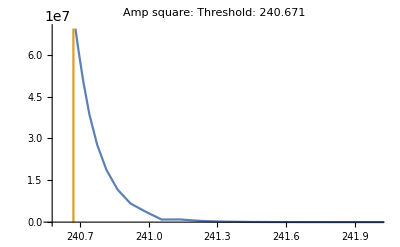

```mathematica
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(Last[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,242},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]]]
```

### Debug

```mathematica
Clear[ValsB,ϕxB,ΦB];
Block[{mQ=60},m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filenameacc,dir,Infinity]=={},If[ChoiceDialog["Choose to use BSW method or not"],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];]
```

Wavefunction build complete.

```mathematica
?ℳ1
```

Global`ℳ1

ℳ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][Ma_,Mb_,Mc_,Md_]:=(#1+𝒮[#1]&)[ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]]+(#1+𝒞[#1]&)[ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]]+(#1+𝒮[#1]+𝒫[#1]+𝒞[#1]&)[ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]]

```mathematica
ParallelTable[ℳ1[ω1,ω2p[ω1][M1,M2,M3,M4]][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4],{ω1,0.1,0.9,0.1}]
```

{1.78558×10^-7,1.65793×10^-6,0.0000101498,0.0000577362,0.000373372,0.00330655,0.0592053,8.32501,889.414}

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
{√S,EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]}]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

{240.681,-6.18205×10^48-1.74609×10^13 ⅈ}

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]]
```

-1.22158×10^87

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]]
```

8225.61

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];If[ω1>1,ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,M2,M1,M3,M4]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2],ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]]+If[ω2>ω1,ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1],ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,M2,M1,M4,M3]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]]
```

15.7

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];If[ω1>1,ℐ1[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1]+ℐ2[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2],ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]]+If[ω2>ω1,ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]+ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000257322,0.999448629114065381444896585261261634514085017144680023193359375}. NIntegrate obtained 1.99029×10^90-1.56519×10^77 ⅈ and 4.57862×10^90 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99969536257832234868968279695167211684747599065303802490234375,0.000552551}. NIntegrate obtained 3.58948×10^89 and 1.95733×10^89 for the integral and error estimates.

-9.397×10^90+9.01471×10^71 ⅈ

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

8319.93

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];
ℐ1[1,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]]
```

0.981933

0.981933

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000257322,0.999448629114065381444896585261261634514085017144680023193359375}. NIntegrate obtained 1.99035×10^90-1.56523×10^77 ⅈ and 4.57875×10^90 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-7.96142×10^90+9.01471×10^71 ⅈ

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000232774,0.99994494132607221035418439830655401578951568808406591415405273437}. NIntegrate obtained 5.68256×10^89-4.46883×10^76 ⅈ and 5.9825×10^89 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999767226318933992235127306003050762228667736053466796875,0.0000550587}. NIntegrate obtained 5.69783×10^89 and 5.9991×10^89 for the integral and error estimates.

-4.55235×10^90+7.64089×10^72 ⅈ

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]]
```

0.981933

0.981933

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000257322,0.999448629114065381444896585261261634514085017144680023193359375}. NIntegrate obtained 1.99029×10^90-1.56519×10^77 ⅈ and 4.57862×10^90 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-7.96119×10^90+9.01471×10^71 ⅈ

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99969536257832234868968279695167211684747599065303802490234375,0.000552551}. NIntegrate obtained 3.58948×10^89 and 1.95733×10^89 for the integral and error estimates.

-1.4358×10^90

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99969536257832234868968279695167211684747599065303802490234375,0.000552551}. NIntegrate obtained 3.58948×10^89 and 1.95733×10^89 for the integral and error estimates.

-1.4358×10^90

```mathematica
λ=10^-5;
```

```mathematica
Table[{x,Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2 (ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)))/λ]},{x,0.,1,0.05}]
```

0.981933

0.981933

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-1.56526×10^-62}. NIntegrate obtained -4.39144×10^192+0. ⅈ and 4.32855×10^192 for the integral and error estimates.

0.981933

0.981933

0.981933

«37 more identical outputs»

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{0.,-4.39144×10^192+0. ⅈ},{0.05,4.00174×10^-9},{0.1,4.77067×10^-8},{0.15,3.75766×10^-7},{0.2,2.90063×10^-6},{0.25,0.0000266597},{0.3,0.000358045},{0.35,0.00995849},{0.4,1.25388},{0.45,788.026},{0.5,-35278.9},{0.55,569.686},{0.6,0.803515},{0.65,0.00767679},{0.7,0.0002967},{0.75,0.0000229902},{0.8,2.56633×10^-6},{0.85,3.38485×10^-7},{0.9,4.35472×10^-8},{0.95,3.69088×10^-9},{1.,0.+0. ⅈ}}

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2)Boole[x>λ],{x,λ,1},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2)Boole[x>λ],{x,λ,1},{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2NIntegrate[ (ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2))Boole[x>λ],{x,λ,1}])/λ]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99969536257832234868968279695167211684747599065303802490234375,0.000552551}. NIntegrate obtained 3.58948×10^89 and 1.95733×10^89 for the integral and error estimates.

3.58951×10^89

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];NIntegrate[NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2 (ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)))/λ,{x,0.01,1},Exclusions->{x==0}]]
```

0.981933

0.981933

NIntegrate::nlim: y = -0.00001+1.0184 x is not a valid limit of integration.

NIntegrate::nlim: y = 0.00001+1.0184 x is not a valid limit of integration.

NIntegrate::nlim: y = -0.00001+1.0184 x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

$Aborted

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4,x=0.},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2 (ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)))/λ]
```

0.981933

0.981933

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-1.56526×10^-62}. NIntegrate obtained -4.39144×10^192+0. ⅈ and 4.32855×10^192 for the integral and error estimates.

-4.39144×10^192+0. ⅈ

```mathematica
Block[{ω1,S,ω2,m=m1,x=1},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];(x+(1+ω2-ω1)/ω1-ω2/ω1)/(1+(1+ω2-ω1)/ω1-ω2/ω1)]
```

0.93123

0.88316

1.

```mathematica
Block[{ω1,S,ω2,m=m1,x=0},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];
(ω2/ω1-((1+1/ω2-ω1/ω2) ω2)/ω1+(x ((1+1/ω2-ω1/ω2) ω2))/ω1)/(ω2/ω1)]
```

0.93123

0.88316

-0.0778682

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
Which[0<ω1<1&&ω2≥ω1,ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1]+ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1],ω2≥ω1&&ω1≥1,ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,M2,M1,M3,M4],0<ω1<1&&ω1>ω2,ℐ3[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,M2,M1,M4,M3],ω1≥1&&ω1>ω2,ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]]
```

-14092.9

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]]
```

4.01135

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m1,M4,M3,M2,M1]]
```

4.01135

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m1,M1,M2,M4,M3]]
```

3.83865

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m1,M3,M4,M2,M1]]
```

3.83865

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m1,M4,M3,M1,M2]]
```

0.981933

-3.35036×10^80+1.31763×10^67 ⅈ

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m1,M3,M4,M1,M2]]
```

4.01135

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][M2,M1,M3,M4]]
```

0

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][M2,M1,M4,M3]]
```

-1.62385

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]]
```

4108.96

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]]
```

4108.96

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]]
```

4108.96

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][M3,M4,M1,M2]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.999409304759193060376486206219937002970254980027675628662109375,0.0000129484} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.26099×10^209 和 2.18188×10^209.

5.04402×10^209

```mathematica
λ=10^-2;
```

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];If[ω1^2+ω2+ω2^2<ω1+2 ω1 ω2,-4 g^2 (NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2 NIntegrate[(ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ),0]]
```

0

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];NIntegrate[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ3[ω1-ω2+x (1-ω1+ω2)] ϕ4[y] ϕ1[x] ϕ2[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,1},MaxRecursion->50]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 2000 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 5.54003×10^6 和 4.90296×10^6.

5.54003×10^6

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];NIntegrate[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ3[ω1-ω2+x (1-ω1+ω2)] ϕ4[y] ϕ1[x] ϕ2[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,(x (1-ω1+ω2))/ω2-λ}]]
```

1.30171×10^183

```mathematica
Block[{ω1,S,ω2,ex},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ex=(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[y] ϕ3[x] ϕ4[1+((-1+y) ω2)/ω1];NIntegrate[ex,{x,0,1},{y,(x (1-ω1+ω2))/ω2+λ,1},MaxRecursion->50,PrecisionGoal->15]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 2000 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -1.10072×10^213 和 2.99925×10^206.

-1.10072×10^213

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];(2 NIntegrate[(ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[(x (1-ω1+ω2))/ω2] ϕ3[x] ϕ4[(x+ω1-x ω1-ω2+x ω2)/ω1])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ]
```

2.68909×10^200

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Plot3D[ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[y] ϕ3[x] ϕ4[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,1},PlotRange->All]]
```

-Graphics3D-

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Plot3D[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2),{x,0,1},{y,0,1},PlotRange->All]]
```

-Graphics3D-

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Plot3D[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[y] ϕ3[x] ϕ4[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,1},PlotRange->All]]
```

-Graphics3D-

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][M2,M1,M4,M3]]
```

2.13307×10^6

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.000590695,0.99998705161026963496755440557323124650679346814285963773727416992} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.25434×10^209-9.59962×10^195 ⅈ 和 2.17036×10^209.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

-5.0174×10^209+4.18059×10^191 ⅈ

```mathematica
Clear[M1,M2,M3,M4,ϕ1,ϕ2,ϕ3,ϕ4]
```

```mathematica
SetSharedVariable[M1,M2,M3,M4,ϕ1,ϕ2,ϕ3,ϕ4]
```

```mathematica
Table[{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[n1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[n2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]],{n1,0,5,1},{n2,0,5,1}]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

$Aborted

```mathematica
ParallelTable[ℳ1[M1,M2,M3,M4][ω1/(ω2p[ω1][M1,M2,M3,M4]),1/(ω2p[ω1][M1,M2,M3,M4])][ϕ1,ϕ2,ϕ3,ϕ4],{ω1,0.1,0.9,0.1}]
```

{3.57115×10^-7,3.31586×10^-6,0.0000202997,0.000115472,0.000746742,0.00661315,0.118411,16.65,1778.83}

```mathematica
?EXPR
```

Global`EXPR

EXPR[ω1_,ω2_][Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]=ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[ω2/(1+ω2-(1+1/ω2-ω1/ω2) ω2),((1+1/ω2-ω1/ω2) ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[1/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2)),(1-ω1+ω2)/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ1[Ma,Mb,Mc,Md][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ1[Ma,Mb,Mc,Md][ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4]

```mathematica
FindRoot[√(Sω1[ω1][M1,M2,M3,M4])==241.137,{ω1,0.9,0.99}]
```

{ω1→0.882942}

```mathematica
Reduce[1/(ω2p[ω1][M1,M2,M3,M4])>(1-ω1+ω2p[ω1][M1,M2,M3,M4])/(ω2p[ω1][M1,M2,M3,M4])&&(1-ω1+ω2p[ω1][M1,M2,M3,M4])/(ω2p[ω1][M1,M2,M3,M4])>1,ω1]
```

$Aborted

```mathematica
Block[{ω1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; ω1/.FindInstance[1/ω2>(1-ω1+ω2)/ω2&&(1-ω1+ω2)/ω2>1&&0<ω1<1,ω1,100]]
```

ω1

```mathematica
Block[{ω1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; ω1/.FindInstance[ω2>ω1&&ω1>1&&0<ω1<1,ω1,100]]
```

ω1

```mathematica
Block[{ω1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; ω1/.FindInstance[(1-ω1+ω2)/ω1>1/ω1&&1/ω1>1&&0<ω1<1,ω1,100]]
```

ω1

```mathematica
ω1/.FindInstance[ω2p[ω1][M1,M2,M3,M4]>ω1&&ω1>1&&0<ω1<1,ω1,100]
```

ω1

```mathematica
Block[{ω1=0.1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; Print[1/ω2>(1-ω1+ω2n[ω1][M1,M2,M3,M4])/(ω2n[ω1][M1,M2,M3,M4])&&(1-ω1+ω2n[ω1][M1,M2,M3,M4])/(ω2n[ω1][M1,M2,M3,M4])>1&&0<ω1<1];NIntegrate[(M3^2+M4^2/(ω1/(1-ω1+ω2))+M1^2/(x-ω2/(1-ω1+ω2))+M1^2/(x-1)-M1^2/(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))-M1^2/x) ϕ1[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[x/(ω2/(1-ω1+ω2))] ϕ3[x] ϕ4[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))],{x,0,1}]]
```

False

8.83407707562666×10^916

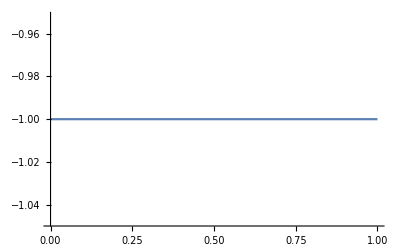

```mathematica
Plot[ω2n[ω1][M1,M2,M3,M4],{ω1,0,1}]
```

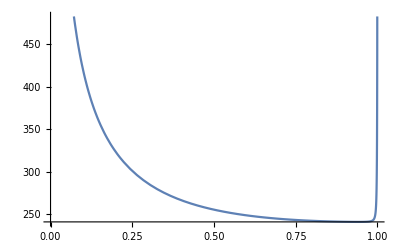

```mathematica
Plot[√(Sω1[ω1][M1,M2,M3,M4]),{ω1,0,1}]
```

```mathematica
Block[{ω1=0.8829424796893336,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];ℳone[ω1,ω2][M1][ϕ1,ϕ2,ϕ3,ϕ4]]
```

1955.93

```mathematica
Block[{ω1=0.907479105147823,ω2,Sen},ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,Print["ω1=",ω1,"    ω2=",ω2];{Sen,ℳone[ω1,ω2][M1][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]]]
```

ω1=0.907479    ω2=0.708776

NIntegrate::ncvb: 在接近 {x,y} = {0.47396,0.589163} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 7087.77 和 143060..

NIntegrate::ncvb: 在接近 {x,y} = {0.526042,0.410879} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 7087.77 和 143060..

{244.244,-113404.}

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];𝒞[ℳ0[ω1,ω2]][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

0.09278

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];ℳ1[M1][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.99972774468308135838688632812676360117620788514614105224609375,9.83724×10^-6} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 4.33383×10^258 和 8.91081×10^258.

-3.46707×10^259

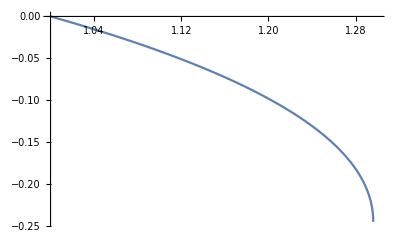

```mathematica
Plot[(ω2p[ω1][M1,M2,M3,M4])/ω1,{ω1,1,1.3}]
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.429446,0.907482} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -9.1960468217209363414030970359671991396517715069998422535022594849×10^1780+6.6644443576245410010334590115150447725581246899922275744416000763×10^1767 ⅈ 和 2.8418655168893182884967858465873180630766840277546920593796254944×10^1780.

-9.19604682172094×10^1780+6.7×10^1767 ⅈ

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,x/ω1+λ,1}]-2/λ NIntegrate[1/ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,0,1}]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.99972774468308135838688632812676360117620788514614105224609375,9.83724×10^-6} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 4.33383×10^258 和 8.91081×10^258.

4.33383×10^258

```mathematica
NI1[ω1_,ω2_][x_?NumberQ]:=NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,0,(ω1-ω2+x ω2)/ω1-λ}]
NI2[ω1_,ω2_][x_?NumberQ]:=NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,(ω1-ω2+x ω2)/ω1+λ,1}]
```

```mathematica
λ=10^-4;
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[NI1[ω1,ω2][x],{x,0,1}]+NIntegrate[NI2[ω1,ω2][x],{x,0,1}]-2/λ NIntegrate[ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}])]
```

$Aborted

```mathematica
Table[Block[{ω1=0.3,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[1/(y-x)^2 ϕ1[x ω2]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,λ,1-λ},{y,0,x-λ}]+NIntegrate[1/(y-x)^2 ϕ1[x ω2]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,λ,1-λ},{y,x+λ,1}]-2/λ NIntegrate[ ϕ1[x ω2]ϕ2[x]ϕ3[x ω1]ϕ4[x],{x,λ,1-λ}])],{λ,Table[10^-m,{m,2,7,1}]}]
```

{19.4562,19.7495,19.7852,19.7698,19.711,19.3019}

-7.96119×10^90+9.01471×10^71 ⅈ